```mathematica
(*Fonctions*)
```

```mathematica
NLegendre[n_,m_,x_]:=Sqrt[Factorial[n-m]*(2n+1)/(2*Factorial[n+m])]*LegendreP[n,m,x];
```

```mathematica
hI[α_,m_,l_,n_]:=NIntegrate[((1-ξ)/2)^α*NLegendre[l,m,ξ]*NLegendre[n,m,ξ],{ξ,-1,1}]
hJ[α_,m_,l_,n_]:=NIntegrate[((1-ξ)/2)^α*((1+ξ)/2)^(-1)*NLegendre[l,m,ξ]*NLegendre[n,m,ξ],{ξ,-1,1}]
```

```mathematica
(*Parameters*)
```

```mathematica
m=2;
ϵ=0.1;
Nbasis=15;
```

```mathematica
(*Matrix elements*)
```

```mathematica
Aln[m_,l_,n_]:=m*Sqrt[1-ϵ]*hI[3/4,m,l,n];
Bln[m_,l_,n_]:=If[l>m,(1/2)*(Sqrt[(2l+1)(l+m+1)(l-m+1)/(2l+3)]*hJ[3/4,m,l+1,n]+hJ[3/4,m,l,n]-Sqrt[(2l+1)(l+m)(l-m)/(2l-1)]*hJ[3/4,m,l-1,n]),(1/2)*(Sqrt[(2l+1)(l+m+1)(l-m+1)/(2l+3)]*hJ[3/4,m,l+1,n]+hJ[3/4,m,l,n])];
Cln[m_,l_,n_]:=m*hJ[3/4,m,l,n];
Dln[m_,l_,n_]:=If[n>m,(1/2)(1/(2n+1)-ϵ/3)*(-Sqrt[(2n+1)(n+m+1)(n-m+1)/(2n+3)]*hI[3/4,m,l,n+1]-hI[3/4,m,l,n]+Sqrt[(2n+1)(n+m)(n-m)/(2n-1)]*hI[3/4,m,l,n-1]),(-Sqrt[(2n+1)(n+m+1)(n-m+1)/(2n+3)]*hI[3/4,m,l,n+1]-hI[3/4,m,l,n])];
Fln[m_,l_,n_]:=2*Sqrt[1-ϵ]*hI[3/4,m,l,n];
Gln[m_,l_,n_]:=-m(1/(2n+1)-ϵ/3)*hI[3/4,m,l,n];
Hln[m_,l_,n_]:=(1/2)*Sqrt[1-ϵ]*(hI[3/4,m,l,n]+3*hI[7/4,m,l,n]);
```

```mathematica
(*Complete matrix*)
```

```mathematica
Mln=ConstantArray[0,{3(Nbasis+1),3(Nbasis+1)}];
For[l=m,l≤m+Nbasis,l++,
For[n=m,n≤m+Nbasis,n++,
(*Aln*)
Mln[[l-m+1,n-m+1]]=Aln[m,l,n];
(*Bln*)
Mln[[l-m+1,n-m+1+(Nbasis+1)]]=Bln[m,l,n];
(*Cln*)
Mln[[l-m+1,n-m+1+2(Nbasis+1)]]=Cln[m,l,n];
(*Dln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1]]=Dln[m,l,n];
(*Aln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1+(Nbasis+1)]]=Aln[m,l,n];
(*Fln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1+2(Nbasis+1)]]=Fln[m,l,n];
(*Gln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1]]=Gln[m,l,n];
(*Hln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1+(Nbasis+1)]]=Hln[m,l,n];
(*Aln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1+2(Nbasis+1)]]=Aln[m,l,n];
]

]
```

```mathematica
LiEgv=Eigenvalues[Mln]
```

{4.17473+0. ⅈ,3.17505+0. ⅈ,1.77827+1.77421 ⅈ,1.77827-1.77421 ⅈ,2.38185+0. ⅈ,2.25237+0. ⅈ,1.66367+1.45869 ⅈ,1.66367-1.45869 ⅈ,0.951582+1.92367 ⅈ,0.951582-1.92367 ⅈ,1.96048+0. ⅈ,1.52703+1.12714 ⅈ,1.52703-1.12714 ⅈ,1.80012+0. ⅈ,1.68883+0. ⅈ,1.3489+0.835823 ⅈ,1.3489-0.835823 ⅈ,1.56178+0. ⅈ,1.43669+0. ⅈ,1.27904+0. ⅈ,1.14937+0.55366 ⅈ,1.14937-0.55366 ⅈ,1.25697+0.200957 ⅈ,1.25697-0.200957 ⅈ,1.05419+0. ⅈ,0.927035+0.349243 ⅈ,0.927035-0.349243 ⅈ,0.845426+0. ⅈ,0.742983+0.214719 ⅈ,0.742983-0.214719 ⅈ,0.637837+0. ⅈ,0.585555+0.147066 ⅈ,0.585555-0.147066 ⅈ,0.473703+0. ⅈ,0.419409+0.106489 ⅈ,0.419409-0.106489 ⅈ,0.367168+0. ⅈ,0.279705+0.0772896 ⅈ,0.279705-0.0772896 ⅈ,0.265909+0. ⅈ,0.17138+0.0421238 ⅈ,0.17138-0.0421238 ⅈ,-0.0610932+0.134422 ⅈ,-0.0610932-0.134422 ⅈ,0.141601+0. ⅈ,0.0938597+0.0151762 ⅈ,0.0938597-0.0151762 ⅈ,0.046981+0. ⅈ}

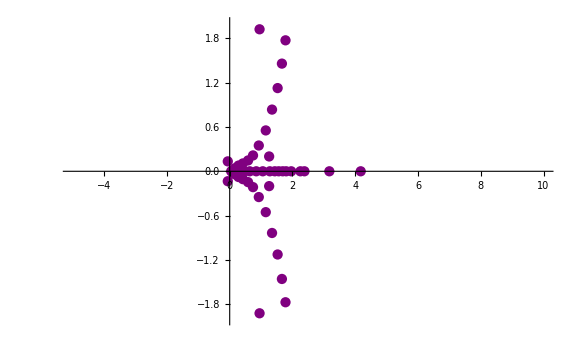

```mathematica
LiEgvRe=Re[LiEgv];
LiEgvIm=Im[LiEgv];
LiEgv2D={LiEgvRe,LiEgvIm}//Transpose;
ListPlot[LiEgv2D,PlotRange->{{-5,10},{-2,2}},PlotStyle->Purple,ImageSize->Large]
```

```mathematica
Mln[[3(25+1),3(25+1)]]
```

1.05758

```mathematica
Mln[[2(30+1)+17,(30+1)+12]]
```

-0.000502198

```mathematica
Fln[m,m,m]
```

1.1115

```mathematica
hI[3/4+1,m-1,m-1+24,m-1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.839875}. NIntegrate obtained 2.07124×10^-8 and 1.51685×10^-11 for the integral and error estimates.

2.07124×10^-8

```mathematica
MatrixForm[Mln]
```

(1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -0.439359 | 1.85129 | -1.77383 | 1.24432 | -0.966752 | 0.770192 | -0.636855 | 0.536195 | -0.460768 | 0.400924 | -0.353456 | 0.314432 | -0.282296 | 0.255172 | -0.232229 | 0.212471 | 3.36842 | -2.71235 | 1.71928 | -1.25748 | 0.962083 | -0.772227 | 0.635844 | -0.536747 | 0.460445 | -0.401123 | 0.353327 | -0.314519 | 0.282236 | -0.255215 | 0.232198 | -0.212493
-0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -1.59297 | -0.429911 | 3.30755 | -3.38645 | 2.53358 | -2.04679 | 1.68084 | -1.42076 | 1.21788 | -1.06146 | 0.934703 | -0.83221 | 0.74668 | -0.675266 | 0.614316 | -0.56222 | -2.71235 | 5.35367 | -4.66425 | 3.29913 | -2.55531 | 2.03881 | -1.68443 | 1.41893 | -1.21891 | 1.06085 | -0.935089 | 0.831955 | -0.746853 | 0.675144 | -0.614404 | 0.562156
-0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | 1.7902 | -3.00446 | -0.42555 | 4.79049 | -5.10329 | 3.98661 | -3.31373 | 2.78448 | -2.39494 | 2.08292 | -1.83679 | 1.63374 | -1.46691 | 1.32588 | -1.20672 | 1.10402 | 1.71928 | -4.66425 | 7.34628 | -6.60281 | 4.98684 | -4.016 | 3.30275 | -2.78951 | 2.39232 | -2.08441 | 1.83588 | -1.63432 | 1.46652 | -1.32615 | 1.20653 | -1.10415
-0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -1.24038 | 3.40814 | -4.46786 | -0.423149 | 6.29775 | -6.89165 | 5.55422 | -4.71833 | 4.03691 | -3.5215 | 3.09956 | -2.76039 | 2.47631 | -2.23969 | 2.0374 | -1.86471 | -1.25748 | 3.29913 | -6.60281 | 9.342 | -8.54916 | 6.74791 | -5.59069 | 4.70457 | -4.04329 | 3.51814 | -3.1015 | 2.7592 | -2.47708 | 2.23917 | -2.03777 | 1.86445
-0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | 0.968153 | -2.52786 | 5.12798 | -5.96462 | -0.421678 | 7.8227 | -8.72949 | 7.20381 | -6.22581 | 5.40484 | -4.77019 | 4.24101 | -3.80888 | 3.44217 | -3.13311 | 2.86627 | 0.962083 | -2.55531 | 4.98684 | -8.54916 | 11.3393 | -10.5045 | 8.55955 | -7.24701 | 6.20941 | -5.41251 | 4.76612 | -4.24337 | 3.80741 | -3.44313 | 3.13247 | -2.86673
-0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.769582 | 2.04896 | -3.97974 | 6.91822 | -7.48323 | -0.420707 | 9.36043 | -10.6028 | 8.9139 | -7.81191 | 6.86381 | -6.11773 | 5.48579 | -4.96281 | 4.51391 | -4.13169 | -0.772227 | 2.03881 | -4.016 | 6.74791 | -10.5045 | 13.3375 | -12.4673 | 10.4073 | -8.96357 | 7.79299 | -6.8727 | 6.11297 | -5.48857 | 4.96108 | -4.51505 | 4.13091
-0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | 0.637159 | -1.67985 | 3.31646 | -5.54654 | 8.75732 | -9.01683 | -0.420031 | 10.9076 | -12.5022 | 10.6699 | -9.45935 | 8.39566 | -7.54616 | 6.81681 | -6.20624 | 5.67684 | 0.635844 | -1.68443 | 3.30275 | -5.59069 | 8.55955 | -12.4673 | 15.3362 | -14.4362 | 12.2817 | -10.7258 | 9.438 | -8.40573 | 7.54076 | -6.81999 | 6.20424 | -5.67816
-0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.53603 | 1.42128 | -2.78318 | 4.72148 | -7.19556 | 10.6315 | -10.5611 | -0.419542 | 12.4619 | -14.4215 | 12.4614 | -11.1555 | 9.98668 | -9.04155 | 8.2204 | -7.52607 | -0.536747 | 1.41893 | -2.78951 | 4.70457 | -7.24701 | 10.4073 | -14.4362 | 17.3352 | -16.4098 | 14.1764 | -12.5236 | 11.1318 | -9.99789 | 9.03552 | -8.22396 | 7.52383
-0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | 0.460865 | -1.21759 | 2.39563 | -4.03537 | 6.22927 | -8.90522 | 12.5316 | -12.1133 | -0.419174 | 14.0216 | -16.3563 | 14.2812 | -12.8911 | 11.6264 | -10.5929 | 9.68554 | 0.460445 | -1.21891 | 2.39232 | -4.04329 | 6.20941 | -8.96357 | 12.2817 | -16.4098 | 19.3345 | -18.3872 | 16.0867 | -14.3494 | 12.8651 | -11.6387 | 10.5863 | -9.68948
-0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.400864 | 1.06164 | -2.08251 | 3.52235 | -5.40311 | 7.81562 | -10.6609 | 14.4514 | -13.6716 | -0.418892 | 15.5857 | -18.3034 | 16.1236 | -14.6589 | 13.3066 | -12.1915 | -0.401123 | 1.06085 | -2.08441 | 3.51814 | -5.41251 | 7.79299 | -10.7258 | 14.1764 | -18.3872 | 21.334 | -20.3677 | 18.0095 | -16.1978 | 14.6306 | -13.32 | 12.1843
-0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | 0.353495 | -0.934591 | 1.83704 | -3.09906 | 4.77116 | -6.86193 | 9.46325 | -12.4522 | 16.3866 | -15.2345 | -0.41867 | 17.1532 | -20.2603 | 17.9846 | -16.4534 | 15.0208 | 0.353327 | -0.935089 | 1.83588 | -3.1015 | 4.76612 | -6.8727 | 9.438 | -12.5236 | 16.0867 | -20.3677 | 23.3335 | -22.3507 | 19.9423 | -18.0647 | 16.4228 | -15.0353
-0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.314406 | 0.832284 | -1.63358 | 2.76071 | -4.24042 | 6.1188 | -8.39365 | 11.1596 | -14.2717 | 18.3339 | -16.8011 | -0.418492 | 18.7236 | -22.2253 | 19.8609 | -18.2703 | -0.314519 | 0.831955 | -1.63432 | 2.7592 | -4.24337 | 6.11297 | -8.40573 | 11.1318 | -14.3494 | 18.0095 | -22.3507 | 25.3332 | -24.3357 | 21.8832 | -19.9469 | 18.2376
-0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | 0.282314 | -0.746629 | 1.46702 | -2.4761 | 3.80925 | -5.48514 | 7.54732 | -9.98457 | 12.8953 | -16.114 | 20.2911 | -18.3707 | -0.418348 | 20.2962 | -24.1969 | 21.7501 | 0.282236 | -0.746853 | 1.46652 | -2.47708 | 3.80741 | -5.48857 | 7.54076 | -9.99789 | 12.8651 | -16.1978 | 19.9423 | -24.3357 | 27.3329 | -26.3224 | 23.831 | -21.8419
-0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.255159 | 0.675302 | -1.3258 | 2.23983 | -3.44192 | 4.96324 | -6.8161 | 9.04278 | -11.6242 | 14.6632 | -17.9748 | 22.2563 | -19.9427 | -0.418228 | 21.8708 | -26.1742 | -0.255215 | 0.675144 | -1.32615 | 2.23917 | -3.44313 | 4.96108 | -6.81999 | 9.03552 | -11.6387 | 14.6306 | -18.0647 | 21.8832 | -26.3224 | 29.3326 | -28.3106 | 25.7844
-0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | 0.232238 | -0.614291 | 1.20677 | -2.0373 | 3.13329 | -4.51362 | 6.2067 | -8.21963 | 10.5942 | -13.3043 | 16.4578 | -19.851 | 24.2281 | -21.5168 | -0.418129 | 23.4469 | 0.232198 | -0.614404 | 1.20653 | -2.03777 | 3.13247 | -4.51505 | 6.20424 | -8.22396 | 10.5863 | -13.32 | 16.4228 | -19.9469 | 23.831 | -28.3106 | 31.3324 | -30.3
-8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.212464 | 0.562239 | -1.10398 | 1.86478 | -2.86615 | 4.13189 | -5.67653 | 7.52657 | -9.68473 | 12.1929 | -15.0185 | 18.2748 | -21.7401 | 26.2055 | -23.0925 | -0.418045 | -0.212493 | 0.562156 | -1.10415 | 1.86445 | -2.86673 | 4.13091 | -5.67816 | 7.52383 | -9.68948 | 12.1843 | -15.0353 | 18.2376 | -21.8419 | 25.7844 | -30.3 | 33.3323
-0.260361 | 0.0961322 | -0.0254573 | -0.00137556 | -0.000277051 | -0.0000808411 | -0.0000285076 | -0.0000112308 | -4.71106×10^-6 | -2.02108×10^-6 | -8.43602×10^-7 | -3.09995×10^-7 | -6.58031×10^-8 | 4.33113×10^-8 | 8.7981×10^-8 | 1.01765×10^-7 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6
-0.91106 | -0.0225366 | 0.0977493 | -0.0284825 | -0.0016586 | -0.000353012 | -0.00010704 | -0.0000386158 | -0.0000153004 | -6.30956×10^-6 | -2.55904×10^-6 | -9.20236×10^-7 | -1.92096×10^-7 | 1.24771×10^-7 | 2.50757×10^-7 | 2.87514×10^-7 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979
0.39277 | -0.0854417 | -0.0182596 | 0.0914105 | -0.0278457 | -0.00167991 | -0.000366575 | -0.000112619 | -0.0000405676 | -0.0000157142 | -6.09952×10^-6 | -2.12377×10^-6 | -4.32588×10^-7 | 2.75647×10^-7 | 5.45581×10^-7 | 6.17837×10^-7 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884
0.0299654 | 0.0363945 | -0.0847928 | -0.0143437 | 0.0828712 | -0.0257557 | -0.00157472 | -0.000345245 | -0.000105246 | -0.0000368852 | -0.0000133972 | -4.45054×10^-6 | -8.75527×10^-7 | 5.43226×10^-7 | 1.05293×10^-6 | 1.17252×10^-6 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527
0.00813667 | 0.00282722 | 0.0358571 | -0.08023 | -0.0112169 | 0.0735445 | -0.0229665 | -0.00140043 | -0.000302948 | -0.0000894615 | -0.0000292982 | -9.08228×10^-6 | -1.7008×10^-6 | 1.01726×10^-6 | 1.91685×10^-6 | 2.08751×10^-6 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698
0.00314042 | 0.000786772 | 0.00281255 | 0.0337427 | -0.073791 | -0.00874901 | 0.0639 | -0.0197995 | -0.0011853 | -0.000247395 | -0.0000680522 | -0.0000189729 | -3.30857×10^-6 | 1.88047×10^-6 | 3.41078×10^-6 | 3.60654×10^-6 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795
0.00145851 | 0.000311346 | 0.000793736 | 0.00266168 | 0.0308975 | -0.0663257 | -0.00677811 | 0.0541214 | -0.0164112 | -0.000944562 | -0.000183105 | -0.0000427762 | -6.69574×10^-6 | 3.53809×10^-6 | 6.08991×10^-6 | 6.1912×10^-6 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473
0.000762569 | 0.000148043 | 0.000318869 | 0.000757769 | 0.00244571 | 0.0276689 | -0.0582456 | -0.00517826 | 0.0442884 | -0.012885 | -0.000687 | -0.000112853 | -0.0000147746 | 6.99697×10^-6 | 0.0000111824 | 0.0000107765 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601
0.000433568 | 0.0000790901 | 0.000153892 | 0.000307422 | 0.000700348 | 0.00219497 | 0.0242216 | -0.0497717 | -0.00385848 | 0.0344377 | -0.00926884 | -0.000417964 | -0.0000384103 | 0.000015192 | 0.0000217336 | 0.0000194269 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453
0.000262568 | 0.0000458551 | 0.0000833878 | 0.000149862 | 0.000286053 | 0.000631092 | 0.00192423 | 0.0206415 | -0.0410324 | -0.00275356 | 0.0245866 | -0.00559172 | -0.000140853 | 0.0000390521 | 0.0000466042 | 0.0000372521 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527
0.000167086 | 0.0000282643 | 0.000048993 | 0.0000820063 | 0.000140436 | 0.000259016 | 0.000554852 | 0.00164132 | 0.0169768 | -0.0321066 | -0.00181632 | 0.0147433 | -0.00187195 | 0.000142095 | 0.00011874 | 0.0000790989 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741
0.000110676 | 0.0000182753 | 0.0000305735 | 0.0000486387 | 0.0000773966 | 0.000127825 | 0.000228542 | 0.000474283 | 0.00135071 | 0.0132562 | -0.0230453 | -0.00101206 | 0.00491128 | 0.00187845 | 0.000429358 | 0.000200098 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448
0.0000757875 | 0.0000122815 | 0.0000199957 | 0.0000306261 | 0.0000462256 | 0.0000708215 | 0.000113228 | 0.000195886 | 0.00039093 | 0.00105508 | 0.00949746 | -0.013883 | -0.000314835 | -0.00490808 | 0.00565133 | 0.000719874 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646
0.0000533721 | 8.52089×10^-6 | 0.0000135804 | 0.0000202006 | 0.0000293036 | 0.000042523 | 0.0000629904 | 0.0000973438 | 0.000161799 | 0.000305735 | 0.000756072 | 0.00571206 | -0.0046433 | 0.000295092 | -0.0147147 | 0.00944104 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317
0.0000384999 | 6.07274×10^-6 | 9.51471×10^-6 | 0.0000138295 | 0.0000194537 | 0.0000270967 | 0.0000379769 | 0.0000543266 | 0.0000805963 | 0.000126748 | 0.000219295 | 0.000454771 | 0.00190764 | 0.00465664 | 0.000832945 | -0.0245091 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291
0.0000283561 | 4.42857×10^-6 | 6.84271×10^-6 | 9.76212×10^-6 | 0.0000134006 | 0.0000180797 | 0.000024299 | 0.0000328606 | 0.0000450946 | 0.0000632565 | 0.000091032 | 0.000132 | 0.000151883 | -0.00191058 | 0.0140044 | 0.00131065 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758
-0.195271 | 0.0377228 | 0.00169716 | 0.00030309 | 0.0000814112 | 0.0000271246 | 0.0000103113 | 4.25996×10^-6 | 1.84563×10^-6 | 8.10296×10^-7 | 3.4407×10^-7 | 1.28104×10^-7 | 2.74738×10^-8 | -1.82323×10^-8 | -3.72844×10^-8 | -4.33639×10^-8 | 0.741001 | -0.358372 | 0.0414016 | 0.000768315 | -0.0000824105 | -0.0000934968 | -0.000061083 | -0.0000380756 | -0.0000240974 | -0.0000156772 | -0.0000104966 | -7.21963×10^-6 | -5.08819×10^-6 | -3.66514×10^-6 | -2.6921×10^-6 | -2.01223×10^-6 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6
0.0574042 | -0.125561 | 0.0314318 | 0.00166549 | 0.000332274 | 0.0000964306 | 0.0000338889 | 0.00001332 | 5.57831×10^-6 | 2.39026×10^-6 | 9.96786×10^-7 | 3.66025×10^-7 | 7.7653×10^-8 | -5.10876×10^-8 | -1.03739×10^-7 | -1.19955×10^-7 | -0.358372 | 0.788807 | -0.412876 | 0.0503465 | 0.00084277 | -0.000183135 | -0.000169178 | -0.00011018 | -0.0000698278 | -0.0000450824 | -0.0000299107 | -0.0000203968 | -0.0000142667 | -0.0000102098 | -7.45744×10^-6 | -5.54751×10^-6 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979
0.00363676 | 0.0442611 | -0.0882622 | 0.0247674 | 0.00143499 | 0.000305443 | 0.0000927114 | 0.000033483 | 0.0000132794 | 5.48055×10^-6 | 2.22428×10^-6 | 8.00292×10^-7 | 1.67133×10^-7 | -1.08598×10^-7 | -2.18323×10^-7 | -2.50392×10^-7 | 0.0414016 | -0.412876 | 0.806082 | -0.435455 | 0.0544401 | 0.000820576 | -0.000273904 | -0.000234769 | -0.000153802 | -0.000098986 | -0.0000649863 | -0.0000438189 | -0.0000303348 | -0.0000215142 | -0.0000155933 | -0.0000115231 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884
0.000877365 | 0.00316818 | 0.0334577 | -0.0649684 | 0.019361 | 0.00118088 | 0.000260773 | 0.0000808928 | 0.0000293588 | 0.0000114388 | 4.46036×10^-6 | 1.5587×10^-6 | 3.18423×10^-7 | -2.03388×10^-7 | -4.0336×10^-7 | -4.5754×10^-7 | 0.000768315 | 0.0503465 | -0.435455 | 0.814289 | -0.447201 | 0.0566677 | 0.000775669 | -0.000349764 | -0.000289643 | -0.000191261 | -0.000124746 | -0.0000830491 | -0.0000567542 | -0.0000397852 | -0.0000285459 | -0.0000209124 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527
0.000311278 | 0.000834874 | 0.00256048 | 0.0255731 | -0.0490155 | 0.0150873 | 0.000945988 | 0.000212297 | 0.000065922 | 0.000023436 | 8.60763×10^-6 | 2.88476×10^-6 | 5.71524×10^-7 | -3.56649×10^-7 | -6.94563×10^-7 | -7.76505×10^-7 | -0.0000824105 | 0.00084277 | 0.0544401 | -0.447201 | 0.818832 | -0.454138 | 0.0580135 | 0.000728835 | -0.000411926 | -0.000335101 | -0.000223032 | -0.000147127 | -0.0000991009 | -0.0000684887 | -0.0000485204 | -0.0000351569 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698
0.000135623 | 0.000316843 | 0.0007127 | 0.0020397 | 0.0197296 | -0.0373962 | 0.0116781 | 0.000739195 | 0.000165369 | 0.0000501535 | 0.0000167711 | 5.2851×10^-6 | 1.00278×10^-6 | -6.06173×10^-7 | -1.15221×10^-6 | -1.26388×10^-6 | -0.0000934968 | -0.000183135 | 0.000820576 | 0.0566677 | -0.454138 | 0.821609 | -0.458592 | 0.0588874 | 0.000686095 | -0.000462786 | -0.000372787 | -0.000249919 | -0.000166461 | -0.000113236 | -0.0000790048 | -0.0000564751 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795
0.0000674199 | 0.000145611 | 0.000282889 | 0.000589019 | 0.00161769 | 0.0152714 | -0.0285512 | 0.00891497 | 0.000559707 | 0.000121907 | 0.0000346982 | 9.93843×10^-6 | 1.77073×10^-6 | -1.02399×10^-6 | -1.88371×10^-6 | -2.01519×10^-6 | -0.000061083 | -0.000169178 | -0.000273904 | 0.000775669 | 0.0580135 | -0.458592 | 0.82343 | -0.461627 | 0.0594862 | 0.000648791 | -0.00050462 | -0.000404194 | -0.00027273 | -0.000183157 | -0.000125644 | -0.0000883776 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473
0.0000367906 | 0.0000755956 | 0.000134947 | 0.000241341 | 0.000479523 | 0.00127679 | 0.0117754 | -0.0215904 | 0.00663869 | 0.000404202 | 0.000082414 | 0.0000200561 | 3.24345×10^-6 | -1.75937×10^-6 | -3.09346×10^-6 | -3.20043×10^-6 | -0.0000380756 | -0.00011018 | -0.000234769 | -0.000349764 | 0.000728835 | 0.0588874 | -0.461627 | 0.824688 | -0.463791 | 0.0599139 | 0.000616742 | -0.000539302 | -0.000430551 | -0.000292175 | -0.000197608 | -0.000136539 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601
0.0000215324 | 0.000042767 | 0.0000722989 | 0.000118325 | 0.000201147 | 0.000385861 | 0.000998692 | 0.00896805 | -0.0159686 | 0.00473523 | 0.000269051 | 0.0000468079 | 6.42209×10^-6 | -3.15839×10^-6 | -5.20443×10^-6 | -5.14263×10^-6 | -0.0000240974 | -0.0000698278 | -0.000153802 | -0.000289643 | -0.000411926 | 0.000686095 | 0.0594862 | -0.463791 | 0.825592 | -0.465389 | 0.0602298 | 0.000589324 | -0.000568301 | -0.000452838 | -0.000308844 | -0.000210163 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453
0.000013312 | 0.000025805 | 0.0000420176 | 0.0000649189 | 0.000100697 | 0.00016479 | 0.000306305 | 0.000768895 | 0.00666798 | -0.0113323 | 0.00312219 | 0.000150984 | 0.0000147842 | -6.16102×10^-6 | -9.19585×10^-6 | -8.50939×10^-6 | -0.0000156772 | -0.0000450824 | -0.000098986 | -0.000191261 | -0.000335101 | -0.000462786 | 0.000648791 | 0.0599139 | -0.465389 | 0.826265 | -0.466604 | 0.0604694 | 0.000565844 | -0.000592757 | -0.000471825 | -0.000323217 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527
8.60175×10^-6 | 0.0000163758 | 0.0000259499 | 0.0000385213 | 0.0000562807 | 0.0000838556 | 0.00013267 | 0.000238567 | 0.000576538 | 0.00475116 | -0.00744302 | 0.00173911 | 0.0000472356 | -0.0000140288 | -0.0000177246 | -0.0000148447 | -0.0000104966 | -0.0000299107 | -0.0000649863 | -0.000124746 | -0.000223032 | -0.000372787 | -0.00050462 | 0.000616742 | 0.0602298 | -0.466604 | 0.826778 | -0.467549 | 0.0606554 | 0.000545665 | -0.000613552 | -0.000488119 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741
5.76468×10^-6 | 0.0000108239 | 0.0000168061 | 0.0000242307 | 0.0000339514 | 0.0000475659 | 0.0000683998 | 0.000104503 | 0.000180545 | 0.000413566 | 0.0031304 | -0.00413326 | 0.000540852 | -0.0000444779 | -0.0000400016 | -0.000028334 | -7.21963×10^-6 | -0.0000203968 | -0.0000438189 | -0.0000830491 | -0.000147127 | -0.000249919 | -0.000404194 | -0.000539302 | 0.000589324 | 0.0604694 | -0.467549 | 0.827179 | -0.468298 | 0.0608025 | 0.000528243 | -0.000631371 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448
3.9837×10^-6 | 7.39922×10^-6 | 0.0000113093 | 0.0000159501 | 0.000021674 | 0.0000290808 | 0.0000392686 | 0.0000544559 | 0.0000798175 | 0.000130486 | 0.000273966 | 0.00174275 | -0.00128229 | -0.000506816 | -0.000126024 | -0.0000634766 | -5.08819×10^-6 | -0.0000142667 | -0.0000303348 | -0.0000567542 | -0.0000991009 | -0.000166461 | -0.00027273 | -0.000430551 | -0.000568301 | 0.000565844 | 0.0606554 | -0.468298 | 0.827497 | -0.468903 | 0.0609209 | 0.000513125 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646
2.826×10^-6 | 5.20364×10^-6 | 7.85524×10^-6 | 0.0000108905 | 0.000014458 | 0.0000187914 | 0.0000242745 | 0.0000315761 | 0.0000419615 | 0.0000581279 | 0.0000869783 | 0.000153202 | 0.000541768 | 0.00119922 | -0.00143029 | -0.000198931 | -3.66514×10^-6 | -0.0000102098 | -0.0000215142 | -0.0000397852 | -0.0000684887 | -0.000113236 | -0.000183157 | -0.000292175 | -0.000452838 | -0.000592757 | 0.000545665 | 0.0608025 | -0.468903 | 0.827755 | -0.469399 | 0.0610175 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317
2.05064×10^-6 | 3.74942×10^-6 | 5.60363×10^-6 | 7.66384×10^-6 | 9.99103×10^-6 | 0.0000126743 | 0.0000158453 | 0.0000197005 | 0.0000245352 | 0.0000307861 | 0.0000389942 | 0.0000488908 | 0.0000478022 | -0.000507521 | 0.00337882 | -0.00225019 | -2.6921×10^-6 | -7.45744×10^-6 | -0.0000155933 | -0.0000285459 | -0.0000485204 | -0.0000790048 | -0.000125644 | -0.000197608 | -0.000308844 | -0.000471825 | -0.000613552 | 0.000528243 | 0.0609209 | -0.469399 | 0.827966 | -0.46981 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291
1.51774×10^-6 | 2.75897×10^-6 | 4.08974×10^-6 | 5.53208×10^-6 | 7.108×10^-6 | 8.84717×10^-6 | 0.0000107872 | 0.0000129702 | 0.0000154279 | 0.0000181287 | 0.0000207826 | 0.0000220376 | 0.0000153219 | -0.0000449198 | -0.00143194 | 0.0053085 | -2.01223×10^-6 | -5.54751×10^-6 | -0.0000115231 | -0.0000209124 | -0.0000351569 | -0.0000564751 | -0.0000883776 | -0.000136539 | -0.000210163 | -0.000323217 | -0.000488119 | -0.000631371 | 0.000513125 | 0.0610175 | -0.46981 | 0.828141 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Dropbox/Mon Mac (MBP-de-admin)/Documents/GitHub/Linear-Galactic-Disk-Theory/code/nb

```mathematica
tabMlnN15eps0dot1=Import["../data/Dump_Matrix.hf5",{"Datasets","tabMln"}]//Transpose;
```

```mathematica
MatrixForm[tabMlnN15eps0dot1]
```

(1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -0.439359 | 1.85129 | -1.77383 | 1.24432 | -0.966752 | 0.770192 | -0.636855 | 0.536195 | -0.460768 | 0.400924 | -0.353456 | 0.314432 | -0.282296 | 0.255172 | -0.232229 | 0.212471 | 3.36842 | -2.71235 | 1.71928 | -1.25748 | 0.962083 | -0.772227 | 0.635844 | -0.536747 | 0.460445 | -0.401123 | 0.353327 | -0.314519 | 0.282236 | -0.255215 | 0.232198 | -0.212493
-0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -1.59297 | -0.429911 | 3.30755 | -3.38645 | 2.53358 | -2.04679 | 1.68084 | -1.42076 | 1.21788 | -1.06146 | 0.934703 | -0.83221 | 0.74668 | -0.675266 | 0.614316 | -0.56222 | -2.71235 | 5.35367 | -4.66425 | 3.29913 | -2.55531 | 2.03881 | -1.68443 | 1.41893 | -1.21891 | 1.06085 | -0.935089 | 0.831955 | -0.746853 | 0.675144 | -0.614404 | 0.562156
-0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | 1.7902 | -3.00446 | -0.42555 | 4.79049 | -5.10329 | 3.98661 | -3.31373 | 2.78448 | -2.39494 | 2.08292 | -1.83679 | 1.63374 | -1.46691 | 1.32588 | -1.20672 | 1.10402 | 1.71928 | -4.66425 | 7.34628 | -6.60281 | 4.98684 | -4.016 | 3.30275 | -2.78951 | 2.39232 | -2.08441 | 1.83588 | -1.63432 | 1.46652 | -1.32615 | 1.20653 | -1.10415
-0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -1.24038 | 3.40814 | -4.46786 | -0.423149 | 6.29775 | -6.89165 | 5.55422 | -4.71833 | 4.03691 | -3.5215 | 3.09956 | -2.76039 | 2.47631 | -2.23969 | 2.0374 | -1.86471 | -1.25748 | 3.29913 | -6.60281 | 9.342 | -8.54916 | 6.74791 | -5.59069 | 4.70457 | -4.04329 | 3.51814 | -3.1015 | 2.7592 | -2.47708 | 2.23917 | -2.03777 | 1.86445
-0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | 0.968153 | -2.52786 | 5.12798 | -5.96462 | -0.421678 | 7.8227 | -8.72949 | 7.20381 | -6.22581 | 5.40484 | -4.77019 | 4.24101 | -3.80888 | 3.44217 | -3.13311 | 2.86627 | 0.962083 | -2.55531 | 4.98684 | -8.54916 | 11.3393 | -10.5045 | 8.55955 | -7.24701 | 6.20941 | -5.41251 | 4.76612 | -4.24337 | 3.80741 | -3.44313 | 3.13247 | -2.86673
-0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.769582 | 2.04896 | -3.97974 | 6.91822 | -7.48323 | -0.420707 | 9.36043 | -10.6028 | 8.9139 | -7.81191 | 6.86381 | -6.11773 | 5.48579 | -4.96281 | 4.51391 | -4.13169 | -0.772227 | 2.03881 | -4.016 | 6.74791 | -10.5045 | 13.3375 | -12.4673 | 10.4073 | -8.96357 | 7.79299 | -6.8727 | 6.11297 | -5.48857 | 4.96108 | -4.51505 | 4.13091
-0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | 0.637159 | -1.67985 | 3.31646 | -5.54654 | 8.75732 | -9.01683 | -0.420031 | 10.9076 | -12.5022 | 10.6699 | -9.45935 | 8.39566 | -7.54616 | 6.81681 | -6.20624 | 5.67684 | 0.635844 | -1.68443 | 3.30275 | -5.59069 | 8.55955 | -12.4673 | 15.3362 | -14.4362 | 12.2817 | -10.7258 | 9.438 | -8.40573 | 7.54076 | -6.81999 | 6.20424 | -5.67816
-0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.53603 | 1.42128 | -2.78318 | 4.72148 | -7.19556 | 10.6315 | -10.5611 | -0.419542 | 12.4619 | -14.4215 | 12.4614 | -11.1555 | 9.98668 | -9.04155 | 8.2204 | -7.52607 | -0.536747 | 1.41893 | -2.78951 | 4.70457 | -7.24701 | 10.4073 | -14.4362 | 17.3352 | -16.4098 | 14.1764 | -12.5236 | 11.1318 | -9.99789 | 9.03552 | -8.22396 | 7.52383
-0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | 0.460865 | -1.21759 | 2.39563 | -4.03537 | 6.22927 | -8.90522 | 12.5316 | -12.1133 | -0.419174 | 14.0216 | -16.3563 | 14.2812 | -12.8911 | 11.6264 | -10.5929 | 9.68554 | 0.460445 | -1.21891 | 2.39232 | -4.04329 | 6.20941 | -8.96357 | 12.2817 | -16.4098 | 19.3345 | -18.3872 | 16.0867 | -14.3494 | 12.8651 | -11.6387 | 10.5863 | -9.68948
-0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.400864 | 1.06164 | -2.08251 | 3.52235 | -5.40311 | 7.81562 | -10.6609 | 14.4514 | -13.6716 | -0.418892 | 15.5857 | -18.3034 | 16.1236 | -14.6589 | 13.3066 | -12.1915 | -0.401123 | 1.06085 | -2.08441 | 3.51814 | -5.41251 | 7.79299 | -10.7258 | 14.1764 | -18.3872 | 21.334 | -20.3677 | 18.0095 | -16.1978 | 14.6306 | -13.32 | 12.1843
-0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | 0.353495 | -0.934591 | 1.83704 | -3.09906 | 4.77116 | -6.86193 | 9.46325 | -12.4522 | 16.3866 | -15.2345 | -0.41867 | 17.1532 | -20.2603 | 17.9846 | -16.4534 | 15.0208 | 0.353327 | -0.935089 | 1.83588 | -3.1015 | 4.76612 | -6.8727 | 9.438 | -12.5236 | 16.0867 | -20.3677 | 23.3335 | -22.3507 | 19.9423 | -18.0647 | 16.4228 | -15.0353
-0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.314406 | 0.832284 | -1.63358 | 2.76071 | -4.24042 | 6.1188 | -8.39365 | 11.1596 | -14.2717 | 18.3339 | -16.8011 | -0.418492 | 18.7236 | -22.2253 | 19.8609 | -18.2703 | -0.314519 | 0.831955 | -1.63432 | 2.7592 | -4.24337 | 6.11297 | -8.40573 | 11.1318 | -14.3494 | 18.0095 | -22.3507 | 25.3332 | -24.3357 | 21.8832 | -19.9469 | 18.2376
-0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | 0.282314 | -0.746629 | 1.46702 | -2.4761 | 3.80925 | -5.48514 | 7.54732 | -9.98457 | 12.8953 | -16.114 | 20.2911 | -18.3707 | -0.418348 | 20.2962 | -24.1969 | 21.7501 | 0.282236 | -0.746853 | 1.46652 | -2.47708 | 3.80741 | -5.48857 | 7.54076 | -9.99789 | 12.8651 | -16.1978 | 19.9423 | -24.3357 | 27.3329 | -26.3224 | 23.831 | -21.8419
-0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.255159 | 0.675302 | -1.3258 | 2.23983 | -3.44192 | 4.96324 | -6.8161 | 9.04278 | -11.6242 | 14.6632 | -17.9748 | 22.2563 | -19.9427 | -0.418228 | 21.8708 | -26.1742 | -0.255215 | 0.675144 | -1.32615 | 2.23917 | -3.44313 | 4.96108 | -6.81999 | 9.03552 | -11.6387 | 14.6306 | -18.0647 | 21.8832 | -26.3224 | 29.3326 | -28.3106 | 25.7844
-0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | 0.232238 | -0.614291 | 1.20677 | -2.0373 | 3.13329 | -4.51362 | 6.2067 | -8.21963 | 10.5942 | -13.3043 | 16.4578 | -19.851 | 24.2281 | -21.5168 | -0.418129 | 23.4469 | 0.232198 | -0.614404 | 1.20653 | -2.03777 | 3.13247 | -4.51505 | 6.20424 | -8.22396 | 10.5863 | -13.32 | 16.4228 | -19.9469 | 23.831 | -28.3106 | 31.3324 | -30.3
-8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.212464 | 0.562239 | -1.10398 | 1.86478 | -2.86615 | 4.13189 | -5.67653 | 7.52657 | -9.68473 | 12.1929 | -15.0185 | 18.2748 | -21.7401 | 26.2055 | -23.0925 | 140.032 | -0.212493 | 0.562156 | -1.10415 | 1.86445 | -2.86673 | 4.13091 | -5.67816 | 7.52383 | -9.68948 | 12.1843 | -15.0353 | 18.2376 | -21.8419 | 25.7844 | -30.3 | 33.3323
-0.0216968 | 0.0961322 | -0.0254573 | -0.00137556 | -0.000277051 | -0.0000808411 | -0.0000285076 | -0.0000112308 | -4.71106×10^-6 | -2.02108×10^-6 | -8.43602×10^-7 | -3.09995×10^-7 | -6.58031×10^-8 | 4.33113×10^-8 | 8.7981×10^-8 | 1.01765×10^-7 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6
-0.0759217 | -0.0225366 | 0.0977493 | -0.0284825 | -0.0016586 | -0.000353012 | -0.00010704 | -0.0000386158 | -0.0000153004 | -6.30956×10^-6 | -2.55904×10^-6 | -9.20236×10^-7 | -1.92096×10^-7 | 1.24771×10^-7 | 2.50757×10^-7 | 2.87514×10^-7 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979
0.0327309 | -0.0854417 | -0.0182596 | 0.0914105 | -0.0278457 | -0.00167991 | -0.000366575 | -0.000112619 | -0.0000405676 | -0.0000157142 | -6.09952×10^-6 | -2.12377×10^-6 | -4.32588×10^-7 | 2.75647×10^-7 | 5.45581×10^-7 | 6.17837×10^-7 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884
0.00249712 | 0.0363945 | -0.0847928 | -0.0143437 | 0.0828712 | -0.0257557 | -0.00157472 | -0.000345245 | -0.000105246 | -0.0000368852 | -0.0000133972 | -4.45054×10^-6 | -8.75527×10^-7 | 5.43226×10^-7 | 1.05293×10^-6 | 1.17252×10^-6 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527
0.000678055 | 0.00282722 | 0.0358571 | -0.08023 | -0.0112169 | 0.0735445 | -0.0229665 | -0.00140043 | -0.000302948 | -0.0000894615 | -0.0000292982 | -9.08228×10^-6 | -1.7008×10^-6 | 1.01726×10^-6 | 1.91685×10^-6 | 2.08751×10^-6 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698
0.000261702 | 0.000786772 | 0.00281255 | 0.0337427 | -0.073791 | -0.00874901 | 0.0639 | -0.0197995 | -0.0011853 | -0.000247395 | -0.0000680522 | -0.0000189729 | -3.30857×10^-6 | 1.88047×10^-6 | 3.41078×10^-6 | 3.60654×10^-6 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795
0.000121542 | 0.000311346 | 0.000793736 | 0.00266168 | 0.0308975 | -0.0663257 | -0.00677811 | 0.0541214 | -0.0164112 | -0.000944562 | -0.000183105 | -0.0000427762 | -6.69574×10^-6 | 3.53809×10^-6 | 6.08991×10^-6 | 6.1912×10^-6 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473
0.0000635474 | 0.000148043 | 0.000318869 | 0.000757769 | 0.00244571 | 0.0276689 | -0.0582456 | -0.00517826 | 0.0442884 | -0.012885 | -0.000687 | -0.000112853 | -0.0000147746 | 6.99697×10^-6 | 0.0000111824 | 0.0000107765 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601
0.0000361306 | 0.0000790901 | 0.000153892 | 0.000307422 | 0.000700348 | 0.00219497 | 0.0242216 | -0.0497717 | -0.00385848 | 0.0344377 | -0.00926884 | -0.000417964 | -0.0000384103 | 0.000015192 | 0.0000217336 | 0.0000194269 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453
0.0000218806 | 0.0000458551 | 0.0000833878 | 0.000149862 | 0.000286053 | 0.000631092 | 0.00192423 | 0.0206415 | -0.0410324 | -0.00275356 | 0.0245866 | -0.00559172 | -0.000140853 | 0.0000390521 | 0.0000466042 | 0.0000372521 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527
0.0000139239 | 0.0000282643 | 0.000048993 | 0.0000820063 | 0.000140436 | 0.000259016 | 0.000554852 | 0.00164132 | 0.0169768 | -0.0321066 | -0.00181632 | 0.0147433 | -0.00187195 | 0.000142095 | 0.00011874 | 0.0000790989 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741
9.22304×10^-6 | 0.0000182753 | 0.0000305735 | 0.0000486387 | 0.0000773966 | 0.000127825 | 0.000228542 | 0.000474283 | 0.00135071 | 0.0132562 | -0.0230453 | -0.00101206 | 0.00491128 | 0.00187845 | 0.000429358 | 0.000200098 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448
6.31562×10^-6 | 0.0000122815 | 0.0000199957 | 0.0000306261 | 0.0000462256 | 0.0000708215 | 0.000113228 | 0.000195886 | 0.00039093 | 0.00105508 | 0.00949746 | -0.013883 | -0.000314835 | -0.00490808 | 0.00565133 | 0.000719874 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646
4.44768×10^-6 | 8.52089×10^-6 | 0.0000135804 | 0.0000202006 | 0.0000293036 | 0.000042523 | 0.0000629904 | 0.0000973438 | 0.000161799 | 0.000305735 | 0.000756072 | 0.00571206 | -0.0046433 | 0.000295092 | -0.0147147 | 0.00944104 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317
3.20832×10^-6 | 6.07274×10^-6 | 9.51471×10^-6 | 0.0000138295 | 0.0000194537 | 0.0000270967 | 0.0000379769 | 0.0000543266 | 0.0000805963 | 0.000126748 | 0.000219295 | 0.000454771 | 0.00190764 | 0.00465664 | 0.000832945 | -0.0245091 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291
2.36301×10^-6 | 4.42857×10^-6 | 6.84271×10^-6 | 9.76212×10^-6 | 0.0000134006 | 0.0000180797 | 0.000024299 | 0.0000328606 | 0.0000450946 | 0.0000632565 | 0.000091032 | 0.000132 | 0.000151883 | -0.00191058 | 0.0140044 | 0.0111076 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758
-0.195271 | 0.0377228 | 0.00169716 | 0.00030309 | 0.0000814112 | 0.0000271246 | 0.0000103113 | 4.25996×10^-6 | 1.84563×10^-6 | 8.10296×10^-7 | 3.4407×10^-7 | 1.28104×10^-7 | 2.74738×10^-8 | -1.82323×10^-8 | -3.72844×10^-8 | -4.33639×10^-8 | 0.741001 | -0.358372 | 0.0414016 | 0.000768315 | -0.0000824105 | -0.0000934968 | -0.000061083 | -0.0000380756 | -0.0000240974 | -0.0000156772 | -0.0000104966 | -7.21963×10^-6 | -5.08819×10^-6 | -3.66514×10^-6 | -2.6921×10^-6 | -2.01223×10^-6 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6
0.0574042 | -0.125561 | 0.0314318 | 0.00166549 | 0.000332274 | 0.0000964306 | 0.0000338889 | 0.00001332 | 5.57831×10^-6 | 2.39026×10^-6 | 9.96786×10^-7 | 3.66025×10^-7 | 7.7653×10^-8 | -5.10876×10^-8 | -1.03739×10^-7 | -1.19955×10^-7 | -0.358372 | 0.788807 | -0.412876 | 0.0503465 | 0.00084277 | -0.000183135 | -0.000169178 | -0.00011018 | -0.0000698278 | -0.0000450824 | -0.0000299107 | -0.0000203968 | -0.0000142667 | -0.0000102098 | -7.45744×10^-6 | -5.54751×10^-6 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979
0.00363676 | 0.0442611 | -0.0882622 | 0.0247674 | 0.00143499 | 0.000305443 | 0.0000927114 | 0.000033483 | 0.0000132794 | 5.48055×10^-6 | 2.22428×10^-6 | 8.00292×10^-7 | 1.67133×10^-7 | -1.08598×10^-7 | -2.18323×10^-7 | -2.50392×10^-7 | 0.0414016 | -0.412876 | 0.806082 | -0.435455 | 0.0544401 | 0.000820576 | -0.000273904 | -0.000234769 | -0.000153802 | -0.000098986 | -0.0000649863 | -0.0000438189 | -0.0000303348 | -0.0000215142 | -0.0000155933 | -0.0000115231 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884
0.000877365 | 0.00316818 | 0.0334577 | -0.0649684 | 0.019361 | 0.00118088 | 0.000260773 | 0.0000808928 | 0.0000293588 | 0.0000114388 | 4.46036×10^-6 | 1.5587×10^-6 | 3.18423×10^-7 | -2.03388×10^-7 | -4.0336×10^-7 | -4.5754×10^-7 | 0.000768315 | 0.0503465 | -0.435455 | 0.814289 | -0.447201 | 0.0566677 | 0.000775669 | -0.000349764 | -0.000289643 | -0.000191261 | -0.000124746 | -0.0000830491 | -0.0000567542 | -0.0000397852 | -0.0000285459 | -0.0000209124 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527
0.000311278 | 0.000834874 | 0.00256048 | 0.0255731 | -0.0490155 | 0.0150873 | 0.000945988 | 0.000212297 | 0.000065922 | 0.000023436 | 8.60763×10^-6 | 2.88476×10^-6 | 5.71524×10^-7 | -3.56649×10^-7 | -6.94563×10^-7 | -7.76505×10^-7 | -0.0000824105 | 0.00084277 | 0.0544401 | -0.447201 | 0.818832 | -0.454138 | 0.0580135 | 0.000728835 | -0.000411926 | -0.000335101 | -0.000223032 | -0.000147127 | -0.0000991009 | -0.0000684887 | -0.0000485204 | -0.0000351569 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698
0.000135623 | 0.000316843 | 0.0007127 | 0.0020397 | 0.0197296 | -0.0373962 | 0.0116781 | 0.000739195 | 0.000165369 | 0.0000501535 | 0.0000167711 | 5.2851×10^-6 | 1.00278×10^-6 | -6.06173×10^-7 | -1.15221×10^-6 | -1.26388×10^-6 | -0.0000934968 | -0.000183135 | 0.000820576 | 0.0566677 | -0.454138 | 0.821609 | -0.458592 | 0.0588874 | 0.000686095 | -0.000462786 | -0.000372787 | -0.000249919 | -0.000166461 | -0.000113236 | -0.0000790048 | -0.0000564751 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795
0.0000674199 | 0.000145611 | 0.000282889 | 0.000589019 | 0.00161769 | 0.0152714 | -0.0285512 | 0.00891497 | 0.000559707 | 0.000121907 | 0.0000346982 | 9.93843×10^-6 | 1.77073×10^-6 | -1.02399×10^-6 | -1.88371×10^-6 | -2.01519×10^-6 | -0.000061083 | -0.000169178 | -0.000273904 | 0.000775669 | 0.0580135 | -0.458592 | 0.82343 | -0.461627 | 0.0594862 | 0.000648791 | -0.00050462 | -0.000404194 | -0.00027273 | -0.000183157 | -0.000125644 | -0.0000883776 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473
0.0000367906 | 0.0000755956 | 0.000134947 | 0.000241341 | 0.000479523 | 0.00127679 | 0.0117754 | -0.0215904 | 0.00663869 | 0.000404202 | 0.000082414 | 0.0000200561 | 3.24345×10^-6 | -1.75937×10^-6 | -3.09346×10^-6 | -3.20043×10^-6 | -0.0000380756 | -0.00011018 | -0.000234769 | -0.000349764 | 0.000728835 | 0.0588874 | -0.461627 | 0.824688 | -0.463791 | 0.0599139 | 0.000616742 | -0.000539302 | -0.000430551 | -0.000292175 | -0.000197608 | -0.000136539 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601
0.0000215324 | 0.000042767 | 0.0000722989 | 0.000118325 | 0.000201147 | 0.000385861 | 0.000998692 | 0.00896805 | -0.0159686 | 0.00473523 | 0.000269051 | 0.0000468079 | 6.42209×10^-6 | -3.15839×10^-6 | -5.20443×10^-6 | -5.14263×10^-6 | -0.0000240974 | -0.0000698278 | -0.000153802 | -0.000289643 | -0.000411926 | 0.000686095 | 0.0594862 | -0.463791 | 0.825592 | -0.465389 | 0.0602298 | 0.000589324 | -0.000568301 | -0.000452838 | -0.000308844 | -0.000210163 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453
0.000013312 | 0.000025805 | 0.0000420176 | 0.0000649189 | 0.000100697 | 0.00016479 | 0.000306305 | 0.000768895 | 0.00666798 | -0.0113323 | 0.00312219 | 0.000150984 | 0.0000147842 | -6.16102×10^-6 | -9.19585×10^-6 | -8.50939×10^-6 | -0.0000156772 | -0.0000450824 | -0.000098986 | -0.000191261 | -0.000335101 | -0.000462786 | 0.000648791 | 0.0599139 | -0.465389 | 0.826265 | -0.466604 | 0.0604694 | 0.000565844 | -0.000592757 | -0.000471825 | -0.000323217 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527
8.60175×10^-6 | 0.0000163758 | 0.0000259499 | 0.0000385213 | 0.0000562807 | 0.0000838556 | 0.00013267 | 0.000238567 | 0.000576538 | 0.00475116 | -0.00744302 | 0.00173911 | 0.0000472356 | -0.0000140288 | -0.0000177246 | -0.0000148447 | -0.0000104966 | -0.0000299107 | -0.0000649863 | -0.000124746 | -0.000223032 | -0.000372787 | -0.00050462 | 0.000616742 | 0.0602298 | -0.466604 | 0.826778 | -0.467549 | 0.0606554 | 0.000545665 | -0.000613552 | -0.000488119 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741
5.76468×10^-6 | 0.0000108239 | 0.0000168061 | 0.0000242307 | 0.0000339514 | 0.0000475659 | 0.0000683998 | 0.000104503 | 0.000180545 | 0.000413566 | 0.0031304 | -0.00413326 | 0.000540852 | -0.0000444779 | -0.0000400016 | -0.000028334 | -7.21963×10^-6 | -0.0000203968 | -0.0000438189 | -0.0000830491 | -0.000147127 | -0.000249919 | -0.000404194 | -0.000539302 | 0.000589324 | 0.0604694 | -0.467549 | 0.827179 | -0.468298 | 0.0608025 | 0.000528243 | -0.000631371 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448
3.9837×10^-6 | 7.39922×10^-6 | 0.0000113093 | 0.0000159501 | 0.000021674 | 0.0000290808 | 0.0000392686 | 0.0000544559 | 0.0000798175 | 0.000130486 | 0.000273966 | 0.00174275 | -0.00128229 | -0.000506816 | -0.000126024 | -0.0000634766 | -5.08819×10^-6 | -0.0000142667 | -0.0000303348 | -0.0000567542 | -0.0000991009 | -0.000166461 | -0.00027273 | -0.000430551 | -0.000568301 | 0.000565844 | 0.0606554 | -0.468298 | 0.827497 | -0.468903 | 0.0609209 | 0.000513125 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646
2.826×10^-6 | 5.20364×10^-6 | 7.85524×10^-6 | 0.0000108905 | 0.000014458 | 0.0000187914 | 0.0000242745 | 0.0000315761 | 0.0000419615 | 0.0000581279 | 0.0000869783 | 0.000153202 | 0.000541768 | 0.00119922 | -0.00143029 | -0.000198931 | -3.66514×10^-6 | -0.0000102098 | -0.0000215142 | -0.0000397852 | -0.0000684887 | -0.000113236 | -0.000183157 | -0.000292175 | -0.000452838 | -0.000592757 | 0.000545665 | 0.0608025 | -0.468903 | 0.827755 | -0.469399 | 0.0610175 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317
2.05064×10^-6 | 3.74942×10^-6 | 5.60363×10^-6 | 7.66384×10^-6 | 9.99103×10^-6 | 0.0000126743 | 0.0000158453 | 0.0000197005 | 0.0000245352 | 0.0000307861 | 0.0000389942 | 0.0000488908 | 0.0000478022 | -0.000507521 | 0.00337882 | -0.00225019 | -2.6921×10^-6 | -7.45744×10^-6 | -0.0000155933 | -0.0000285459 | -0.0000485204 | -0.0000790048 | -0.000125644 | -0.000197608 | -0.000308844 | -0.000471825 | -0.000613552 | 0.000528243 | 0.0609209 | -0.469399 | 0.827966 | -0.46981 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291
1.51774×10^-6 | 2.75897×10^-6 | 4.08974×10^-6 | 5.53208×10^-6 | 7.108×10^-6 | 8.84717×10^-6 | 0.0000107872 | 0.0000129702 | 0.0000154279 | 0.0000181287 | 0.0000207826 | 0.0000220376 | 0.0000153219 | -0.0000449198 | -0.00143194 | 0.0053085 | -2.01223×10^-6 | -5.54751×10^-6 | -0.0000115231 | -0.0000209124 | -0.0000351569 | -0.0000564751 | -0.0000883776 | -0.000136539 | -0.000210163 | -0.000323217 | -0.000488119 | -0.000631371 | 0.000513125 | 0.0610175 | -0.46981 | 0.828141 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758)

```mathematica
MatrixForm[tabMlnN15eps0dot1-Mln]
```

(1.16413×10^-10 | 2.28956×10^-11 | 3.3166×10^-12 | -1.81279×10^-16 | 1.22732×10^-16 | 4.4127×10^-17 | 2.53161×10^-17 | 1.13841×10^-16 | 1.76183×10^-18 | 4.14369×10^-16 | 1.31157×10^-15 | 4.76588×10^-16 | -6.06869×10^-15 | 7.01744×10^-15 | -1.02151×10^-15 | -7.53181×10^-15 | 5.69517×10^-10 | 5.18405×10^-10 | 1.08305×10^-9 | 1.2985×10^-10 | 2.09105×10^-10 | 3.17895×10^-10 | 3.93202×10^-10 | 4.11168×10^-11 | 5.50045×10^-11 | 7.21369×10^-11 | 9.30748×10^-11 | 1.9525×10^-11 | -4.62408×10^-14 | -1.45051×10^-13 | -4.46865×10^-15 | 2.44915×10^-13 | 1.6501×10^-9 | 3.32291×10^-10 | 6.94206×10^-10 | 8.48699×10^-11 | 1.36659×10^-10 | 2.0776×10^-10 | 1.97784×10^-11 | 2.71402×10^-11 | 3.63042×10^-11 | 4.75929×10^-11 | 6.14291×10^-11 | 7.82794×10^-11 | 5.52891×10^-14 | -8.88734×10^-14 | 4.01623×10^-14 | 6.30329×10^-14
2.28956×10^-11 | 6.20324×10^-11 | 1.25725×10^-10 | 3.1572×10^-16 | 3.03577×10^-17 | 1.7911×10^-16 | -1.04083×10^-17 | -2.08058×10^-16 | 1.15088×10^-16 | -1.27003×10^-15 | -1.52149×10^-15 | -1.4138×10^-15 | 9.12387×10^-15 | -2.13143×10^-14 | -5.85944×10^-15 | 3.29115×10^-14 | -4.78156×10^-10 | 1.48085×10^-9 | 2.24786×10^-10 | 3.57296×10^-10 | 5.75368×10^-10 | 6.02478×10^-11 | 2.73083×10^-10 | 1.10969×10^-10 | 1.48444×10^-10 | 1.94644×10^-10 | 2.51193×10^-10 | -5.16909×10^-11 | 8.90399×10^-14 | 3.27627×10^-13 | 3.01426×10^-13 | -2.39919×10^-12 | 3.32291×10^-10 | 9.21425×10^-10 | 1.92505×10^-9 | 2.29933×10^-10 | 3.70278×10^-10 | 5.6292×10^-10 | 8.21787×10^-10 | 7.26668×10^-11 | 9.72122×10^-11 | 1.27501×10^-10 | 1.64497×10^-10 | -9.4813×10^-14 | -1.27121×10^-13 | -2.60125×10^-13 | -3.05311×10^-14 | 4.85056×10^-13
3.3166×10^-12 | 1.25725×10^-10 | 2.54814×10^-10 | 3.05163×10^-11 | 3.81639×10^-17 | -1.31839×10^-16 | 7.97973×10^-17 | 2.96638×10^-16 | -5.68989×10^-16 | 1.3263×10^-15 | 3.5261×10^-15 | 4.13759×10^-16 | -1.9323×10^-14 | 2.48483×10^-14 | 7.7116×10^-15 | -1.80853×10^-14 | -6.48026×10^-11 | -1.85286×10^-10 | -1.34106×10^-9 | 7.38735×10^-10 | 1.18972×10^-9 | -4.01082×10^-10 | -5.91903×10^-10 | 2.23723×10^-10 | 2.99296×10^-10 | 3.92509×10^-10 | 5.06566×10^-10 | -5.59552×10^-14 | 3.28404×10^-13 | -3.06422×10^-13 | 6.66356×10^-13 | -7.97584×10^-13 | 6.94206×10^-10 | 1.92505×10^-9 | 2.65394×10^-10 | 4.66047×10^-10 | 7.50481×10^-10 | 7.45493×10^-11 | 1.05687×10^-10 | 1.45012×10^-10 | 1.93979×10^-10 | 2.54331×10^-10 | 3.28244×10^-10 | 1.43885×10^-13 | 2.06057×10^-13 | 4.37428×10^-13 | 4.39426×10^-13 | -3.24563×10^-12
-1.81279×10^-16 | 3.1572×10^-16 | 3.05163×10^-11 | 5.25624×10^-11 | 8.27414×10^-11 | 3.19189×10^-16 | 8.1532×10^-17 | -3.72966×10^-16 | 5.87204×10^-16 | -2.14954×10^-15 | -2.08568×10^-15 | 1.58402×10^-16 | 1.47446×10^-14 | -4.21619×10^-14 | -1.6478×10^-14 | 3.58177×10^-14 | -6.80257×10^-10 | -1.89901×10^-9 | 7.56666×10^-10 | 1.32875×10^-9 | 2.14011×10^-9 | 2.0064×10^-10 | 2.84449×10^-10 | 3.90303×10^-10 | 5.22169×10^-10 | 6.84802×10^-10 | 8.83782×10^-10 | 1.46549×10^-14 | -5.40901×10^-13 | 5.05374×10^-13 | 4.47198×10^-13 | -2.87348×10^-12 | 8.48699×10^-11 | 2.29933×10^-10 | 4.66047×10^-10 | 8.1833×10^-10 | 1.3179×10^-9 | 1.284×10^-10 | 1.82052×10^-10 | 2.49766×10^-10 | 3.34141×10^-10 | 4.38233×10^-10 | 5.65524×10^-10 | -1.78968×10^-13 | 1.46549×10^-13 | -6.47482×10^-13 | 5.08482×10^-13 | 4.73177×10^-13
1.22732×10^-16 | 3.03577×10^-17 | 3.81639×10^-17 | 8.27414×10^-11 | 1.30244×10^-10 | 2.77556×10^-16 | -1.04083×10^-16 | 3.34802×10^-16 | -4.34548×10^-16 | 1.57947×10^-15 | 1.99038×10^-15 | -9.43906×10^-16 | -1.78134×10^-14 | 2.9295×10^-14 | 1.83961×10^-14 | 4.95271×10^-14 | 2.28049×10^-10 | 6.17926×10^-10 | -4.12496×10^-10 | -7.28173×10^-10 | -1.17994×10^-9 | 3.20526×10^-10 | 4.5449×10^-10 | 6.23591×10^-10 | 8.34361×10^-10 | 1.09429×10^-9 | -6.46765×10^-10 | 7.62057×10^-13 | 2.14495×10^-13 | 1.08358×10^-13 | 7.61169×10^-13 | 7.55929×10^-12 | 1.36659×10^-10 | 3.70278×10^-10 | 7.50481×10^-10 | 1.3179×10^-9 | 2.12252×10^-9 | 2.02141×10^-10 | 2.86569×10^-10 | 3.93214×10^-10 | 5.26041×10^-10 | 6.89814×10^-10 | 8.90271×10^-10 | 1.85629×10^-13 | -2.42917×10^-13 | 9.38361×10^-13 | 6.73683×10^-13 | -5.45963×10^-12
4.4127×10^-17 | 1.7911×10^-16 | -1.31839×10^-16 | 3.19189×10^-16 | 2.77556×10^-16 | 2.85739×10^-10 | 6.66134×10^-16 | 5.82867×10^-16 | 4.19803×10^-16 | -1.55344×10^-15 | -3.15286×10^-16 | 2.47176×10^-15 | 7.52501×10^-15 | -2.89604×10^-14 | -1.78402×10^-14 | -4.3607×10^-14 | -1.58265×10^-10 | 9.68539×10^-10 | -1.14106×10^-9 | -2.01087×10^-9 | -3.25178×10^-9 | 4.82856×10^-10 | 6.84588×10^-10 | 9.3949×10^-10 | 1.25705×10^-9 | 1.64901×10^-9 | -1.60369×10^-9 | -9.04166×10^-13 | 3.73035×10^-14 | 2.20268×10^-13 | -2.54907×10^-12 | -6.79456×10^-13 | 2.0776×10^-10 | 5.6292×10^-10 | 7.45493×10^-11 | 1.284×10^-10 | 2.02141×10^-10 | 2.99373×10^-10 | 4.24491×10^-10 | 5.82405×10^-10 | 7.79224×10^-10 | 1.02199×10^-9 | 7.19425×10^-14 | 2.82441×10^-13 | 3.20632×10^-13 | -7.18536×10^-13 | 8.80185×10^-13 | 6.18261×10^-12
2.53161×10^-17 | -1.04083×10^-17 | 7.97973×10^-17 | 8.1532×10^-17 | -1.04083×10^-16 | 6.66134×10^-16 | -1.77636×10^-15 | 8.88178×10^-16 | 7.56339×10^-16 | 1.13277×10^-15 | -1.48319×10^-15 | -4.07183×10^-15 | 7.84312×10^-16 | 1.35162×10^-14 | 1.20958×10^-14 | 2.42791×10^-14 | -3.67045×10^-10 | -8.04254×10^-10 | 1.73644×10^-10 | 2.99092×10^-10 | 4.70868×10^-10 | 6.97479×10^-10 | 9.89051×10^-10 | 1.35726×10^-9 | 1.81644×10^-9 | -1.74465×10^-9 | -2.43361×10^-13 | 1.66978×10^-13 | -2.27374×10^-13 | -8.52651×10^-13 | -8.65086×10^-13 | -1.56639×10^-11 | 1.97784×10^-11 | 8.21787×10^-10 | 1.05687×10^-10 | 1.82052×10^-10 | 2.86569×10^-10 | 4.24491×10^-10 | 6.01808×10^-10 | 8.25853×10^-10 | 1.10492×10^-9 | 1.44923×10^-9 | 3.19744×10^-14 | -3.51719×10^-13 | -2.63789×10^-13 | 1.1493×10^-12 | -8.55316×10^-13 | -6.63114×10^-12
1.13841×10^-16 | -2.08058×10^-16 | 2.96638×10^-16 | -3.72966×10^-16 | 3.34802×10^-16 | 5.82867×10^-16 | 8.88178×10^-16 | -8.88178×10^-16 | 3.33067×10^-16 | -1.45717×10^-15 | 1.73472×10^-17 | 5.35422×10^-15 | -1.80194×10^-15 | 6.14743×10^-16 | -2.13666×10^-14 | -9.38922×10^-14 | 4.55012×10^-11 | -1.66122×10^-9 | 2.43103×10^-10 | 4.18751×10^-10 | 6.59334×10^-10 | 9.76659×10^-10 | 1.38515×10^-9 | 1.90106×10^-9 | 2.54437×10^-9 | 2.84164×10^-9 | -3.19744×10^-14 | 8.88178×10^-14 | 2.4869×10^-14 | 4.06786×10^-13 | 6.86384×10^-12 | 1.30473×10^-11 | 2.71402×10^-11 | 7.26668×10^-11 | 1.45012×10^-10 | 2.49766×10^-10 | 3.93214×10^-10 | 5.82405×10^-10 | 8.25853×10^-10 | 1.13319×10^-9 | 1.51639×10^-9 | -3.55271×10^-14 | -4.9738×10^-14 | 4.03233×10^-13 | 2.39808×10^-13 | -1.26299×10^-12 | 5.61329×10^-13 | -6.06626×10^-13
1.76183×10^-18 | 1.15088×10^-16 | -5.68989×10^-16 | 5.87204×10^-16 | -4.34548×10^-16 | 4.19803×10^-16 | 7.56339×10^-16 | 3.33067×10^-16 | -2.44249×10^-15 | 4.71845×10^-15 | 7.28584×10^-15 | -6.0299×10^-15 | 3.68715×10^-15 | 6.6544×10^-15 | 3.68995×10^-14 | 2.1295×10^-14 | 6.21614×10^-11 | 1.66624×10^-10 | 3.32236×10^-10 | 5.72696×10^-10 | 9.01334×10^-10 | 1.33574×10^-9 | 1.8942×10^-9 | -2.53919×10^-9 | 3.48117×10^-9 | 6.6499×10^-10 | 2.91323×10^-13 | -4.33431×10^-13 | 2.20268×10^-13 | 1.75149×10^-12 | -7.01661×10^-12 | 2.37321×10^-12 | 3.63042×10^-11 | 9.72122×10^-11 | 1.93979×10^-10 | 3.34141×10^-10 | 5.26041×10^-10 | 7.79224×10^-10 | 1.10492×10^-9 | 1.51639×10^-9 | 2.02916×10^-9 | 2.66218×10^-9 | 2.4869×10^-14 | -3.57048×10^-13 | -2.78888×10^-13 | 1.45484×10^-12 | 2.03393×10^-12 | -9.3614×10^-13
4.14369×10^-16 | -1.27003×10^-15 | 1.3263×10^-15 | -2.14954×10^-15 | 1.57947×10^-15 | -1.55344×10^-15 | 1.13277×10^-15 | -1.45717×10^-15 | 4.71845×10^-15 | -1.9984×10^-15 | -9.4369×10^-16 | 8.03524×10^-15 | 4.92835×10^-15 | -1.01048×10^-14 | -5.77611×10^-14 | 2.0896×10^-14 | 8.34472×10^-11 | 2.23484×10^-10 | 4.45931×10^-10 | 7.68471×10^-10 | 1.20968×10^-9 | -1.94951×10^-9 | -2.76455×10^-9 | -4.29155×10^-9 | -5.07693×10^-9 | -7.53388×10^-9 | 4.68958×10^-13 | 0. | 8.52651×10^-14 | -2.75691×10^-12 | 1.34648×10^-12 | -1.1724×10^-13 | 4.75929×10^-11 | 1.27501×10^-10 | 2.54331×10^-10 | 4.38233×10^-10 | 6.89814×10^-10 | 1.02199×10^-9 | 1.44923×10^-9 | -3.55271×10^-14 | 2.66218×10^-9 | -2.52243×10^-13 | 5.68434×10^-14 | 2.73559×10^-13 | 3.48166×10^-13 | -7.21201×10^-13 | -2.35367×10^-12 | 4.06786×10^-13
1.31157×10^-15 | -1.52149×10^-15 | 3.5261×10^-15 | -2.08568×10^-15 | 1.99038×10^-15 | -3.15286×10^-16 | -1.48319×10^-15 | 1.73472×10^-17 | 7.28584×10^-15 | -9.4369×10^-16 | 8.21565×10^-15 | -1.28231×10^-14 | -5.2458×10^-15 | 1.63983×10^-14 | 7.51569×10^-14 | -8.46476×10^-14 | 1.10472×10^-10 | -3.52377×10^-10 | -7.01843×10^-10 | -1.21067×10^-9 | -1.90423×10^-9 | -3.15089×10^-9 | -4.47045×10^-9 | 1.35358×10^-12 | -8.21118×10^-9 | 1.64846×10^-12 | -1.3074×10^-12 | 4.9738×10^-13 | -5.18696×10^-13 | 1.03739×10^-12 | -1.7053×10^-13 | 2.45848×10^-12 | 6.14291×10^-11 | 1.64497×10^-10 | 3.28244×10^-10 | 5.65524×10^-10 | 8.90271×10^-10 | 7.19425×10^-14 | 3.19744×10^-14 | -4.9738×10^-14 | 2.4869×10^-14 | 5.68434×10^-14 | 1.81188×10^-13 | -3.8014×10^-13 | -2.80664×10^-13 | 5.40012×10^-13 | 2.71427×10^-12 | -1.00897×10^-12
4.76588×10^-16 | -1.4138×10^-15 | 4.13759×10^-16 | 1.58402×10^-16 | -9.43906×10^-16 | 2.47176×10^-15 | -4.07183×10^-15 | 5.35422×10^-15 | -6.0299×10^-15 | 8.03524×10^-15 | -1.28231×10^-14 | 1.08802×10^-14 | 1.02696×10^-14 | -3.37994×10^-14 | -6.39072×10^-14 | 1.52573×10^-13 | -1.85252×10^-10 | -5.49424×10^-10 | -1.09472×10^-9 | -1.88687×10^-9 | -2.97185×10^-9 | 9.02389×10^-13 | -1.07292×10^-12 | 1.06226×10^-12 | -1.10134×10^-12 | 1.03739×10^-12 | -1.62714×10^-12 | 2.06057×10^-12 | 4.83169×10^-13 | -1.67688×10^-12 | -1.93268×10^-12 | -1.1724×10^-12 | 7.82794×10^-11 | -9.4813×10^-14 | 1.43885×10^-13 | -1.78968×10^-13 | 1.85629×10^-13 | 2.82441×10^-13 | -3.51719×10^-13 | 4.03233×10^-13 | -3.57048×10^-13 | 2.73559×10^-13 | -3.8014×10^-13 | 4.68958×10^-13 | 2.06057×10^-13 | -4.33431×10^-13 | -2.62546×10^-12 | 1.28608×10^-12
-6.06869×10^-15 | 9.12387×10^-15 | -1.9323×10^-14 | 1.47446×10^-14 | -1.78134×10^-14 | 7.52501×10^-15 | 7.84312×10^-16 | -1.80194×10^-15 | 3.68715×10^-15 | 4.92835×10^-15 | -5.2458×10^-15 | 1.02696×10^-14 | -3.17524×10^-14 | 3.64153×10^-14 | 7.6647×10^-14 | -1.07581×10^-13 | -2.81337×10^-10 | -6.2661×10^-13 | 1.10933×10^-12 | -1.64935×10^-12 | 2.64855×10^-12 | -3.52074×10^-12 | 5.32552×10^-12 | -5.94014×10^-12 | 6.45883×10^-12 | -3.48166×10^-12 | 3.24007×10^-12 | -3.18323×10^-12 | -4.9738×10^-13 | 4.17799×10^-12 | 3.6664×10^-12 | 1.97531×10^-12 | 5.52891×10^-14 | -1.27121×10^-13 | 2.06057×10^-13 | 1.46549×10^-13 | -2.42917×10^-13 | 3.20632×10^-13 | -2.63789×10^-13 | 2.39808×10^-13 | -2.78888×10^-13 | 3.48166×10^-13 | -2.80664×10^-13 | 2.06057×10^-13 | -1.49214×10^-13 | 6.75016×10^-14 | 2.32703×10^-12 | -1.45306×10^-12
7.01744×10^-15 | -2.13143×10^-14 | 2.48483×10^-14 | -4.21619×10^-14 | 2.9295×10^-14 | -2.89604×10^-14 | 1.35162×10^-14 | 6.14743×10^-16 | 6.6544×10^-15 | -1.01048×10^-14 | 1.63983×10^-14 | -3.37994×10^-14 | 3.64153×10^-14 | -1.86517×10^-14 | -4.996×10^-14 | 1.58006×10^-13 | -8.01581×10^-14 | 3.06422×10^-13 | 1.00719×10^-12 | 1.23013×10^-12 | 3.76055×10^-12 | 1.97176×10^-12 | -1.98952×10^-12 | 9.20153×10^-13 | 9.25837×10^-12 | -1.05658×10^-11 | 1.16387×10^-11 | -1.09992×10^-11 | 9.54969×10^-12 | -6.86384×10^-12 | -7.44649×10^-12 | 8.7681×10^-12 | -8.88734×10^-14 | -2.60125×10^-13 | 4.37428×10^-13 | -6.47482×10^-13 | 9.38361×10^-13 | -7.18536×10^-13 | 1.1493×10^-12 | -1.26299×10^-12 | 1.45484×10^-12 | -7.21201×10^-13 | 5.40012×10^-13 | -4.33431×10^-13 | 6.75016×10^-14 | 7.28306×10^-13 | -1.7657×10^-12 | 1.93268×10^-12
-1.02151×10^-15 | -5.85944×10^-15 | 7.7116×10^-15 | -1.6478×10^-14 | 1.83961×10^-14 | -1.78402×10^-14 | 1.20958×10^-14 | -2.13666×10^-14 | 3.68995×10^-14 | -5.77611×10^-14 | 7.51569×10^-14 | -6.39072×10^-14 | 7.6647×10^-14 | -4.996×10^-14 | -3.33067×10^-14 | 1.28786×10^-14 | 6.32494×10^-13 | 3.04601×10^-12 | -1.49818×10^-11 | 4.718×10^-12 | -2.60503×10^-11 | 2.84999×10^-11 | -3.20988×10^-11 | 2.83151×10^-12 | -9.27969×10^-12 | 4.02878×10^-12 | -5.67724×10^-12 | 6.4091×10^-12 | -5.68434×10^-12 | 4.51905×10^-12 | 1.02318×10^-11 | -1.88862×10^-11 | 4.01623×10^-14 | -3.05311×10^-14 | 4.39426×10^-13 | 5.08482×10^-13 | 6.73683×10^-13 | 8.80185×10^-13 | -8.55316×10^-13 | 5.61329×10^-13 | 2.03393×10^-12 | -2.35367×10^-12 | 2.71427×10^-12 | -2.62546×10^-12 | 2.32703×10^-12 | -1.7657×10^-12 | 5.04485×10^-13 | 6.99885×10^-13
-7.53181×10^-15 | 3.29115×10^-14 | -1.80853×10^-14 | 3.58177×10^-14 | 4.95271×10^-14 | -4.3607×10^-14 | 2.42791×10^-14 | -9.38922×10^-14 | 2.1295×10^-14 | 2.0896×10^-14 | -8.46476×10^-14 | 1.52573×10^-13 | -1.07581×10^-13 | 1.58006×10^-13 | 1.28786×10^-14 | -1.37002×10^-13 | 9.36584×10^-13 | -2.76179×10^-12 | 3.57137×10^-12 | -1.17559×10^-11 | 3.83338×10^-12 | -1.35589×10^-11 | 7.21911×10^-12 | 1.58629×10^-11 | -3.49232×10^-11 | 5.61968×10^-11 | -7.93108×10^-11 | 9.37916×10^-11 | -9.17595×10^-11 | 7.66391×10^-11 | -4.33857×10^-11 | 140.45 | 6.30329×10^-14 | 4.85056×10^-13 | -3.24563×10^-12 | 4.73177×10^-13 | -5.45963×10^-12 | 6.18261×10^-12 | -6.63114×10^-12 | -6.06626×10^-13 | -9.3614×10^-13 | 4.06786×10^-13 | -1.00897×10^-12 | 1.28608×10^-12 | -1.45306×10^-12 | 1.93268×10^-12 | 6.99885×10^-13 | -2.73559×10^-12
0.238664 | 7.93628×10^-12 | 1.77531×10^-12 | 2.54932×10^-13 | -1.74014×10^-17 | 5.75982×10^-18 | -4.06915×10^-18 | 5.33631×10^-19 | -1.17162×10^-17 | -4.08486×10^-17 | -3.67295×10^-18 | 9.58156×10^-17 | -2.66515×10^-17 | 2.39657×10^-17 | -1.91192×10^-16 | 4.63663×10^-16 | 1.16413×10^-10 | 2.28956×10^-11 | 3.3166×10^-12 | -1.81279×10^-16 | 1.22732×10^-16 | 4.4127×10^-17 | 2.53161×10^-17 | 1.13841×10^-16 | 1.76183×10^-18 | 4.14369×10^-16 | 1.31157×10^-15 | 4.76588×10^-16 | -6.06869×10^-15 | 7.01744×10^-15 | -1.02151×10^-15 | -7.53181×10^-15 | 1.16413×10^-10 | 2.28956×10^-11 | 3.3166×10^-12 | -1.81279×10^-16 | 1.22732×10^-16 | 4.4127×10^-17 | 2.53161×10^-17 | 1.13841×10^-16 | 1.76183×10^-18 | 4.14369×10^-16 | 1.31157×10^-15 | 4.76588×10^-16 | -6.06869×10^-15 | 7.01744×10^-15 | -1.02151×10^-15 | -7.53181×10^-15
0.835139 | -1.11279×10^-11 | 2.41718×10^-12 | 9.6642×10^-12 | 8.89046×10^-18 | 9.75782×10^-19 | 2.16027×10^-17 | -4.88569×10^-18 | 4.09117×10^-17 | 5.30421×10^-17 | 5.85003×10^-18 | -1.37504×10^-16 | 8.39158×10^-17 | -7.1322×10^-17 | 7.04917×10^-16 | -6.33301×10^-16 | 2.28956×10^-11 | 6.20324×10^-11 | 1.25725×10^-10 | 3.1572×10^-16 | 3.03577×10^-17 | 1.7911×10^-16 | -1.04083×10^-17 | -2.08058×10^-16 | 1.15088×10^-16 | -1.27003×10^-15 | -1.52149×10^-15 | -1.4138×10^-15 | 9.12387×10^-15 | -2.13143×10^-14 | -5.85944×10^-15 | 3.29115×10^-14 | 2.28956×10^-11 | 6.20324×10^-11 | 1.25725×10^-10 | 3.1572×10^-16 | 3.03577×10^-17 | 1.7911×10^-16 | -1.04083×10^-17 | -2.08058×10^-16 | 1.15088×10^-16 | -1.27003×10^-15 | -1.52149×10^-15 | -1.4138×10^-15 | 9.12387×10^-15 | -2.13143×10^-14 | -5.85944×10^-15 | 3.29115×10^-14
-0.360039 | -2.58437×10^-11 | 2.30648×10^-12 | 1.91239×10^-11 | 2.1557×10^-12 | -8.67362×10^-19 | -2.43945×10^-17 | 2.92328×10^-17 | -3.79471×10^-17 | -1.27753×10^-16 | 1.35644×10^-17 | 2.9769×10^-16 | -1.00568×10^-16 | 1.24818×10^-16 | -5.55579×10^-16 | 5.96538×10^-15 | 3.3166×10^-12 | 1.25725×10^-10 | 2.54814×10^-10 | 3.05163×10^-11 | 3.81639×10^-17 | -1.31839×10^-16 | 7.97973×10^-17 | 2.96638×10^-16 | -5.68989×10^-16 | 1.3263×10^-15 | 3.5261×10^-15 | 4.13759×10^-16 | -1.9323×10^-14 | 2.48483×10^-14 | 7.7116×10^-15 | -1.80853×10^-14 | 3.3166×10^-12 | 1.25725×10^-10 | 2.54814×10^-10 | 3.05163×10^-11 | 3.81639×10^-17 | -1.31839×10^-16 | 7.97973×10^-17 | 2.96638×10^-16 | -5.68989×10^-16 | 1.3263×10^-15 | 3.5261×10^-15 | 4.13759×10^-16 | -1.9323×10^-14 | 2.48483×10^-14 | 7.7116×10^-15 | -1.80853×10^-14
-0.0274683 | -2.69081×10^-12 | -5.09108×10^-12 | -4.9843×10^-12 | 2.76255×10^-12 | 5.23722×10^-12 | 3.77302×10^-17 | -2.21177×10^-17 | 6.69495×10^-17 | 8.67972×10^-17 | -4.63581×10^-17 | -2.19733×10^-16 | 1.79848×10^-16 | -1.48003×10^-16 | 1.00715×10^-15 | -7.0557×10^-15 | -1.81279×10^-16 | 3.1572×10^-16 | 3.05163×10^-11 | 5.25624×10^-11 | 8.27414×10^-11 | 3.19189×10^-16 | 8.1532×10^-17 | -3.72966×10^-16 | 5.87204×10^-16 | -2.14954×10^-15 | -2.08568×10^-15 | 1.58402×10^-16 | 1.47446×10^-14 | -4.21619×10^-14 | -1.6478×10^-14 | 3.58177×10^-14 | -1.81279×10^-16 | 3.1572×10^-16 | 3.05163×10^-11 | 5.25624×10^-11 | 8.27414×10^-11 | 3.19189×10^-16 | 8.1532×10^-17 | -3.72966×10^-16 | 5.87204×10^-16 | -2.14954×10^-15 | -2.08568×10^-15 | 1.58402×10^-16 | 1.47446×10^-14 | -4.21619×10^-14 | -1.6478×10^-14 | 3.58177×10^-14
-0.00745861 | 5.20417×10^-18 | -7.02962×10^-12 | -1.15383×10^-11 | 4.34877×10^-12 | 8.24392×10^-12 | -3.46945×10^-18 | 1.40946×10^-17 | -4.6946×10^-17 | -7.77915×10^-17 | 5.12353×10^-17 | 2.59309×10^-16 | -1.26297×10^-16 | 1.66085×10^-16 | 2.79861×10^-16 | 9.06853×10^-15 | 1.22732×10^-16 | 3.03577×10^-17 | 3.81639×10^-17 | 8.27414×10^-11 | 1.30244×10^-10 | 2.77556×10^-16 | -1.04083×10^-16 | 3.34802×10^-16 | -4.34548×10^-16 | 1.57947×10^-15 | 1.99038×10^-15 | -9.43906×10^-16 | -1.78134×10^-14 | 2.9295×10^-14 | 1.83961×10^-14 | 4.95271×10^-14 | 1.22732×10^-16 | 3.03577×10^-17 | 3.81639×10^-17 | 8.27414×10^-11 | 1.30244×10^-10 | 2.77556×10^-16 | -1.04083×10^-16 | 3.34802×10^-16 | -4.34548×10^-16 | 1.57947×10^-15 | 1.99038×10^-15 | -9.43906×10^-16 | -1.78134×10^-14 | 2.9295×10^-14 | 1.83961×10^-14 | 4.95271×10^-14
-0.00287872 | 9.86624×10^-18 | -9.1073×10^-18 | -4.16334×10^-17 | -2.04977×10^-11 | -2.50999×10^-12 | 1.58276×10^-11 | 6.93889×10^-18 | 8.13152×10^-17 | 2.64003×10^-17 | -8.67768×10^-17 | -1.04707×10^-16 | 1.34603×10^-16 | -1.18758×10^-16 | -2.06298×10^-16 | -6.05683×10^-15 | 4.4127×10^-17 | 1.7911×10^-16 | -1.31839×10^-16 | 3.19189×10^-16 | 2.77556×10^-16 | 2.85739×10^-10 | 6.66134×10^-16 | 5.82867×10^-16 | 4.19803×10^-16 | -1.55344×10^-15 | -3.15286×10^-16 | 2.47176×10^-15 | 7.52501×10^-15 | -2.89604×10^-14 | -1.78402×10^-14 | -4.3607×10^-14 | 4.4127×10^-17 | 1.7911×10^-16 | -1.31839×10^-16 | 3.19189×10^-16 | 2.77556×10^-16 | 2.85739×10^-10 | 6.66134×10^-16 | 5.82867×10^-16 | 4.19803×10^-16 | -1.55344×10^-15 | -3.15286×10^-16 | 2.47176×10^-15 | 7.52501×10^-15 | -2.89604×10^-14 | -1.78402×10^-14 | -4.3607×10^-14
-0.00133697 | -4.8247×10^-18 | -9.54098×10^-18 | 1.25767×10^-17 | -4.16334×10^-17 | 1.11022×10^-16 | -2.60209×10^-18 | -1.11022×10^-16 | -1.04083×10^-17 | 6.49437×10^-17 | 1.15603×10^-16 | -2.55804×10^-17 | -7.68149×10^-17 | 5.31488×10^-17 | 1.507×10^-16 | 7.32865×10^-15 | 2.53161×10^-17 | -1.04083×10^-17 | 7.97973×10^-17 | 8.1532×10^-17 | -1.04083×10^-16 | 6.66134×10^-16 | -1.77636×10^-15 | 8.88178×10^-16 | 7.56339×10^-16 | 1.13277×10^-15 | -1.48319×10^-15 | -4.07183×10^-15 | 7.84312×10^-16 | 1.35162×10^-14 | 1.20958×10^-14 | 2.42791×10^-14 | 2.53161×10^-17 | -1.04083×10^-17 | 7.97973×10^-17 | 8.1532×10^-17 | -1.04083×10^-16 | 6.66134×10^-16 | -1.77636×10^-15 | 8.88178×10^-16 | 7.56339×10^-16 | 1.13277×10^-15 | -1.48319×10^-15 | -4.07183×10^-15 | 7.84312×10^-16 | 1.35162×10^-14 | 1.20958×10^-14 | 2.42791×10^-14
-0.000699021 | -1.15196×10^-17 | 8.83625×10^-18 | 2.1684×10^-18 | -7.1991×10^-17 | -4.51028×10^-17 | 8.32667×10^-17 | 2.77556×10^-17 | 2.77556×10^-17 | 1.38778×10^-17 | -1.47668×10^-16 | 1.85128×10^-17 | 2.11606×10^-17 | -8.51294×10^-17 | -1.25418×10^-15 | -4.91469×10^-15 | 1.13841×10^-16 | -2.08058×10^-16 | 2.96638×10^-16 | -3.72966×10^-16 | 3.34802×10^-16 | 5.82867×10^-16 | 8.88178×10^-16 | -8.88178×10^-16 | 3.33067×10^-16 | -1.45717×10^-15 | 1.73472×10^-17 | 5.35422×10^-15 | -1.80194×10^-15 | 6.14743×10^-16 | -2.13666×10^-14 | -9.38922×10^-14 | 1.13841×10^-16 | -2.08058×10^-16 | 2.96638×10^-16 | -3.72966×10^-16 | 3.34802×10^-16 | 5.82867×10^-16 | 8.88178×10^-16 | -8.88178×10^-16 | 3.33067×10^-16 | -1.45717×10^-15 | 1.73472×10^-17 | 5.35422×10^-15 | -1.80194×10^-15 | 6.14743×10^-16 | -2.13666×10^-14 | -9.38922×10^-14
-0.000397437 | 4.69731×10^-17 | -2.89482×10^-17 | -1.82688×10^-17 | 1.64799×10^-17 | -7.89299×10^-17 | 0. | 1.45717×10^-16 | -1.59595×10^-16 | -2.98372×10^-16 | 2.22045×10^-16 | 5.2638×10^-17 | -5.63311×10^-17 | 1.46699×10^-16 | 2.21194×10^-16 | -1.30911×10^-15 | 1.76183×10^-18 | 1.15088×10^-16 | -5.68989×10^-16 | 5.87204×10^-16 | -4.34548×10^-16 | 4.19803×10^-16 | 7.56339×10^-16 | 3.33067×10^-16 | -2.44249×10^-15 | 4.71845×10^-15 | 7.28584×10^-15 | -6.0299×10^-15 | 3.68715×10^-15 | 6.6544×10^-15 | 3.68995×10^-14 | 2.1295×10^-14 | 1.76183×10^-18 | 1.15088×10^-16 | -5.68989×10^-16 | 5.87204×10^-16 | -4.34548×10^-16 | 4.19803×10^-16 | 7.56339×10^-16 | 3.33067×10^-16 | -2.44249×10^-15 | 4.71845×10^-15 | 7.28584×10^-15 | -6.0299×10^-15 | 3.68715×10^-15 | 6.6544×10^-15 | 3.68995×10^-14 | 2.1295×10^-14
-0.000240687 | -4.864×10^-17 | 5.31801×10^-17 | 9.86624×10^-18 | -5.86011×10^-17 | 4.10913×10^-17 | -1.23599×10^-17 | -1.63064×10^-16 | 6.93889×10^-18 | 1.76074×10^-16 | -2.25514×10^-16 | -8.41341×10^-17 | 7.74391×10^-17 | -2.76153×10^-16 | 3.59569×10^-16 | 7.64419×10^-15 | 4.14369×10^-16 | -1.27003×10^-15 | 1.3263×10^-15 | -2.14954×10^-15 | 1.57947×10^-15 | -1.55344×10^-15 | 1.13277×10^-15 | -1.45717×10^-15 | 4.71845×10^-15 | -1.9984×10^-15 | -9.4369×10^-16 | 8.03524×10^-15 | 4.92835×10^-15 | -1.01048×10^-14 | -5.77611×10^-14 | 2.0896×10^-14 | 4.14369×10^-16 | -1.27003×10^-15 | 1.3263×10^-15 | -2.14954×10^-15 | 1.57947×10^-15 | -1.55344×10^-15 | 1.13277×10^-15 | -1.45717×10^-15 | 4.71845×10^-15 | -1.9984×10^-15 | -9.4369×10^-16 | 8.03524×10^-15 | 4.92835×10^-15 | -1.01048×10^-14 | -5.77611×10^-14 | 2.0896×10^-14
-0.000153162 | -1.66849×10^-16 | -1.75641×10^-17 | 1.45568×10^-16 | -1.47614×10^-16 | 2.23617×10^-16 | -8.45678×10^-18 | -4.15249×10^-16 | 1.38778×10^-17 | -1.38778×10^-17 | 2.46331×10^-16 | 1.8735×10^-16 | -1.25984×10^-16 | 3.5513×10^-16 | -1.26251×10^-15 | -1.30718×10^-14 | 1.31157×10^-15 | -1.52149×10^-15 | 3.5261×10^-15 | -2.08568×10^-15 | 1.99038×10^-15 | -3.15286×10^-16 | -1.48319×10^-15 | 1.73472×10^-17 | 7.28584×10^-15 | -9.4369×10^-16 | 8.21565×10^-15 | -1.28231×10^-14 | -5.2458×10^-15 | 1.63983×10^-14 | 7.51569×10^-14 | -8.46476×10^-14 | 1.31157×10^-15 | -1.52149×10^-15 | 3.5261×10^-15 | -2.08568×10^-15 | 1.99038×10^-15 | -3.15286×10^-16 | -1.48319×10^-15 | 1.73472×10^-17 | 7.28584×10^-15 | -9.4369×10^-16 | 8.21565×10^-15 | -1.28231×10^-14 | -5.2458×10^-15 | 1.63983×10^-14 | 7.51569×10^-14 | -8.46476×10^-14
-0.000101453 | 4.07152×10^-17 | -1.35756×10^-16 | 1.03907×10^-16 | -1.55285×10^-16 | 1.78758×10^-16 | -1.34224×10^-16 | 6.657×10^-17 | -8.21825×10^-17 | 1.8735×10^-16 | -4.16334×10^-17 | -3.12033×10^-16 | 1.91687×10^-16 | -3.33067×10^-16 | 2.38823×10^-15 | 1.38307×10^-14 | 4.76588×10^-16 | -1.4138×10^-15 | 4.13759×10^-16 | 1.58402×10^-16 | -9.43906×10^-16 | 2.47176×10^-15 | -4.07183×10^-15 | 5.35422×10^-15 | -6.0299×10^-15 | 8.03524×10^-15 | -1.28231×10^-14 | 1.08802×10^-14 | 1.02696×10^-14 | -3.37994×10^-14 | -6.39072×10^-14 | 1.52573×10^-13 | 4.76588×10^-16 | -1.4138×10^-15 | 4.13759×10^-16 | 1.58402×10^-16 | -9.43906×10^-16 | 2.47176×10^-15 | -4.07183×10^-15 | 5.35422×10^-15 | -6.0299×10^-15 | 8.03524×10^-15 | -1.28231×10^-14 | 1.08802×10^-14 | 1.02696×10^-14 | -3.37994×10^-14 | -6.39072×10^-14 | 1.52573×10^-13
-0.0000694719 | 9.77059×10^-16 | -1.22091×10^-16 | -3.02635×10^-16 | 7.06358×10^-16 | -1.24374×10^-15 | 5.12014×10^-16 | -1.28559×10^-16 | -2.75604×10^-16 | 2.57606×10^-16 | -1.09288×10^-16 | 3.33067×10^-16 | -1.04571×10^-16 | 4.8312×10^-16 | -1.82233×10^-15 | -1.99333×10^-14 | -6.06869×10^-15 | 9.12387×10^-15 | -1.9323×10^-14 | 1.47446×10^-14 | -1.78134×10^-14 | 7.52501×10^-15 | 7.84312×10^-16 | -1.80194×10^-15 | 3.68715×10^-15 | 4.92835×10^-15 | -5.2458×10^-15 | 1.02696×10^-14 | -3.17524×10^-14 | 3.64153×10^-14 | 7.6647×10^-14 | -1.07581×10^-13 | -6.06869×10^-15 | 9.12387×10^-15 | -1.9323×10^-14 | 1.47446×10^-14 | -1.78134×10^-14 | 7.52501×10^-15 | 7.84312×10^-16 | -1.80194×10^-15 | 3.68715×10^-15 | 4.92835×10^-15 | -5.2458×10^-15 | 1.02696×10^-14 | -3.17524×10^-14 | 3.64153×10^-14 | 7.6647×10^-14 | -1.07581×10^-13
-0.0000489244 | -1.03996×10^-15 | 1.35676×10^-15 | 2.36861×10^-16 | -1.23735×10^-15 | 1.24477×10^-15 | -1.72923×10^-15 | 3.19121×10^-16 | 3.91939×10^-16 | -2.69045×10^-16 | 4.86265×10^-16 | -2.28983×10^-16 | -7.63278×10^-17 | -3.81802×10^-16 | 2.27596×10^-15 | 1.43878×10^-14 | 7.01744×10^-15 | -2.13143×10^-14 | 2.48483×10^-14 | -4.21619×10^-14 | 2.9295×10^-14 | -2.89604×10^-14 | 1.35162×10^-14 | 6.14743×10^-16 | 6.6544×10^-15 | -1.01048×10^-14 | 1.63983×10^-14 | -3.37994×10^-14 | 3.64153×10^-14 | -1.86517×10^-14 | -4.996×10^-14 | 1.58006×10^-13 | 7.01744×10^-15 | -2.13143×10^-14 | 2.48483×10^-14 | -4.21619×10^-14 | 2.9295×10^-14 | -2.89604×10^-14 | 1.35162×10^-14 | 6.14743×10^-16 | 6.6544×10^-15 | -1.01048×10^-14 | 1.63983×10^-14 | -3.37994×10^-14 | 3.64153×10^-14 | -1.86517×10^-14 | -4.996×10^-14 | 1.58006×10^-13
-0.0000352915 | -5.88859×10^-16 | 7.70163×10^-16 | -6.09613×10^-16 | -9.55419×10^-17 | 5.48024×10^-16 | 1.2183×10^-16 | -1.06956×10^-15 | 1.28002×10^-15 | -1.00923×10^-15 | 3.93023×10^-18 | 4.13623×10^-17 | -8.39172×10^-17 | -4.93529×10^-16 | 7.93528×10^-16 | -1.37494×10^-14 | -1.02151×10^-15 | -5.85944×10^-15 | 7.7116×10^-15 | -1.6478×10^-14 | 1.83961×10^-14 | -1.78402×10^-14 | 1.20958×10^-14 | -2.13666×10^-14 | 3.68995×10^-14 | -5.77611×10^-14 | 7.51569×10^-14 | -6.39072×10^-14 | 7.6647×10^-14 | -4.996×10^-14 | -3.33067×10^-14 | 1.28786×10^-14 | -1.02151×10^-15 | -5.85944×10^-15 | 7.7116×10^-15 | -1.6478×10^-14 | 1.83961×10^-14 | -1.78402×10^-14 | 1.20958×10^-14 | -2.13666×10^-14 | 3.68995×10^-14 | -5.77611×10^-14 | 7.51569×10^-14 | -6.39072×10^-14 | 7.6647×10^-14 | -4.996×10^-14 | -3.33067×10^-14 | 1.28786×10^-14
-0.0000259931 | 6.96303×10^-17 | -2.27225×10^-17 | -5.84383×10^-15 | 5.08944×10^-15 | 1.96616×10^-15 | 2.65641×10^-15 | 6.13631×10^-16 | -4.53421×10^-15 | 3.15686×10^-15 | -2.71158×10^-15 | 1.52086×10^-16 | 8.07731×10^-18 | 5.68989×10^-16 | -3.85456×10^-15 | 0.00979693 | -7.53181×10^-15 | 3.29115×10^-14 | -1.80853×10^-14 | 3.58177×10^-14 | 4.95271×10^-14 | -4.3607×10^-14 | 2.42791×10^-14 | -9.38922×10^-14 | 2.1295×10^-14 | 2.0896×10^-14 | -8.46476×10^-14 | 1.52573×10^-13 | -1.07581×10^-13 | 1.58006×10^-13 | 1.28786×10^-14 | -1.37002×10^-13 | -7.53181×10^-15 | 3.29115×10^-14 | -1.80853×10^-14 | 3.58177×10^-14 | 4.95271×10^-14 | -4.3607×10^-14 | 2.42791×10^-14 | -9.38922×10^-14 | 2.1295×10^-14 | 2.0896×10^-14 | -8.46476×10^-14 | 1.52573×10^-13 | -1.07581×10^-13 | 1.58006×10^-13 | 1.28786×10^-14 | -1.37002×10^-13
-2.04517×10^-11 | -2.64325×10^-12 | -2.71911×10^-13 | 1.10047×10^-17 | -5.63785×10^-18 | -1.55176×10^-18 | -6.81014×10^-19 | -2.31579×10^-18 | -2.64698×10^-20 | -4.43115×10^-18 | -9.21667×10^-18 | -1.86061×10^-18 | 7.35283×10^-18 | 7.9538×10^-18 | -3.26292×10^-18 | -3.78058×10^-17 | -3.00688×10^-11 | -9.80882×10^-14 | 4.10845×10^-13 | -2.5954×10^-14 | -4.05349×10^-14 | 2.12775×10^-18 | 3.00053×10^-17 | 8.53199×10^-17 | 1.81807×10^-17 | 1.92341×10^-16 | 8.53193×10^-16 | 5.35669×10^-16 | -3.01135×10^-15 | 8.11489×10^-15 | 7.73001×10^-16 | -2.63031×10^-15 | 1.16413×10^-10 | 2.28956×10^-11 | 3.3166×10^-12 | -1.81279×10^-16 | 1.22732×10^-16 | 4.4127×10^-17 | 2.53161×10^-17 | 1.13841×10^-16 | 1.76183×10^-18 | 4.14369×10^-16 | 1.31157×10^-15 | 4.76588×10^-16 | -6.06869×10^-15 | 7.01744×10^-15 | -1.02151×10^-15 | -7.53181×10^-15
-4.02235×10^-12 | -7.16155×10^-12 | -1.03076×10^-11 | -1.88651×10^-17 | -1.40946×10^-18 | -6.30193×10^-18 | 2.71051×10^-19 | 4.23008×10^-18 | -1.73303×10^-18 | 1.35813×10^-17 | 1.06919×10^-17 | 5.51953×10^-18 | -1.10545×10^-17 | -2.41583×10^-17 | -1.87163×10^-17 | 1.65199×10^-16 | -9.80882×10^-14 | -6.46816×10^-13 | -2.37116×10^-12 | -1.99208×10^-12 | -1.08567×10^-13 | 9.69006×10^-17 | -4.14436×10^-17 | -4.70815×10^-17 | 7.94991×10^-17 | -6.47458×10^-16 | -1.52699×10^-15 | 1.23403×10^-15 | 5.39896×10^-15 | -1.52886×10^-14 | -6.00339×10^-15 | 6.41166×10^-15 | 2.28956×10^-11 | 6.20324×10^-11 | 1.25725×10^-10 | 3.1572×10^-16 | 3.03577×10^-17 | 1.7911×10^-16 | -1.04083×10^-17 | -2.08058×10^-16 | 1.15088×10^-16 | -1.27003×10^-15 | -1.52149×10^-15 | -1.4138×10^-15 | 9.12387×10^-15 | -2.13143×10^-14 | -5.85944×10^-15 | 3.29115×10^-14
-5.82666×10^-13 | -1.45148×10^-11 | -2.08909×10^-11 | -1.85204×10^-12 | -1.95156×10^-18 | 4.60786×10^-18 | -2.15485×10^-18 | -6.03765×10^-18 | 8.56859×10^-18 | -1.41827×10^-17 | -2.47787×10^-17 | -1.61529×10^-18 | 2.34118×10^-17 | 2.81638×10^-17 | 2.46326×10^-17 | -9.07787×10^-17 | 4.10845×10^-13 | -2.37116×10^-12 | -7.10954×10^-12 | 3.58785×10^-12 | -6.51763×10^-12 | -3.21194×10^-13 | 5.51317×10^-17 | -1.18991×10^-16 | -2.82706×10^-16 | 1.11079×10^-15 | 2.58716×10^-15 | -3.2427×10^-15 | -1.00039×10^-14 | 2.24062×10^-14 | 8.60751×10^-15 | 3.01595×10^-15 | 3.3166×10^-12 | 1.25725×10^-10 | 2.54814×10^-10 | 3.05163×10^-11 | 3.81639×10^-17 | -1.31839×10^-16 | 7.97973×10^-17 | 2.96638×10^-16 | -5.68989×10^-16 | 1.3263×10^-15 | 3.5261×10^-15 | 4.13759×10^-16 | -1.9323×10^-14 | 2.48483×10^-14 | 7.7116×10^-15 | -1.80853×10^-14
3.17671×10^-17 | -3.64292×10^-17 | -2.50188×10^-12 | -3.19×10^-12 | -3.80177×10^-12 | -1.10589×10^-17 | -2.22261×10^-18 | 7.57586×10^-18 | -8.84302×10^-18 | 2.29851×10^-17 | 1.46562×10^-17 | -6.18334×10^-19 | -1.78646×10^-17 | -4.77876×10^-17 | -5.26343×10^-17 | 1.79786×10^-16 | -2.5954×10^-14 | -1.99208×10^-12 | 3.58785×10^-12 | 6.03384×10^-12 | 9.21918×10^-12 | -5.53203×10^-13 | 1.02457×10^-16 | -2.05998×10^-18 | 3.94921×10^-16 | -1.86426×10^-15 | -2.20838×10^-15 | 5.07678×10^-15 | 1.33872×10^-14 | -3.09859×10^-14 | -1.44527×10^-14 | -6.66026×10^-15 | -1.81279×10^-16 | 3.1572×10^-16 | 3.05163×10^-11 | 5.25624×10^-11 | 8.27414×10^-11 | 3.19189×10^-16 | 8.1532×10^-17 | -3.72966×10^-16 | 5.87204×10^-16 | -2.14954×10^-15 | -2.08568×10^-15 | 1.58402×10^-16 | 1.47446×10^-14 | -4.21619×10^-14 | -1.6478×10^-14 | 3.58177×10^-14
-2.15214×10^-17 | -3.36103×10^-18 | -3.03577×10^-18 | -5.02159×10^-12 | -5.98439×10^-12 | -1.04083×10^-17 | 2.81893×10^-18 | -6.80337×10^-18 | 6.55942×10^-18 | -1.68898×10^-17 | -1.39862×10^-17 | 3.68544×10^-18 | 2.15827×10^-17 | 3.32039×10^-17 | 5.87613×10^-17 | 2.48601×10^-16 | -4.05349×10^-14 | -1.08567×10^-13 | -6.51763×10^-12 | 9.21918×10^-12 | 1.4044×10^-11 | -2.82581×10^-11 | -1.23722×10^-12 | -1.66967×10^-16 | -4.4783×10^-16 | 2.03667×10^-15 | 1.82046×10^-15 | -6.38728×10^-15 | -1.33166×10^-14 | 3.04214×10^-14 | 1.65196×10^-14 | 3.98815×10^-14 | 1.22732×10^-16 | 3.03577×10^-17 | 3.81639×10^-17 | 8.27414×10^-11 | 1.30244×10^-10 | 2.77556×10^-16 | -1.04083×10^-16 | 3.34802×10^-16 | -4.34548×10^-16 | 1.57947×10^-15 | 1.99038×10^-15 | -9.43906×10^-16 | -1.78134×10^-14 | 2.9295×10^-14 | 1.83961×10^-14 | 4.95271×10^-14
-7.75205×10^-18 | -2.07083×10^-17 | 1.0842×10^-17 | -1.9082×10^-17 | -1.38778×10^-17 | -1.00399×10^-11 | -1.73472×10^-17 | -1.17094×10^-17 | -6.31548×10^-18 | 1.66154×10^-17 | 2.21584×10^-18 | -9.65025×10^-18 | -9.11746×10^-18 | -3.28246×10^-17 | -5.69856×10^-17 | -2.18885×10^-16 | 2.12775×10^-18 | 9.69006×10^-17 | -3.21194×10^-13 | -5.53203×10^-13 | -2.82581×10^-11 | 7.0142×10^-11 | -1.83376×10^-12 | 3.05311×10^-16 | 3.71881×10^-16 | -2.00003×10^-15 | -4.80464×10^-16 | 7.04585×10^-15 | 7.22103×10^-15 | -2.31576×10^-14 | -1.49021×10^-14 | -4.71282×10^-14 | 4.4127×10^-17 | 1.7911×10^-16 | -1.31839×10^-16 | 3.19189×10^-16 | 2.77556×10^-16 | 2.85739×10^-10 | 6.66134×10^-16 | 5.82867×10^-16 | 4.19803×10^-16 | -1.55344×10^-15 | -3.15286×10^-16 | 2.47176×10^-15 | 7.52501×10^-15 | -2.89604×10^-14 | -1.78402×10^-14 | -4.3607×10^-14
-4.45878×10^-18 | 1.19262×10^-18 | -6.55942×10^-18 | -4.98733×10^-18 | 4.77049×10^-18 | -2.42861×10^-17 | 4.51028×10^-17 | -1.73472×10^-17 | -1.13841×10^-17 | -1.21295×10^-17 | 1.04287×10^-17 | 1.58954×10^-17 | -9.50159×10^-19 | 1.53196×10^-17 | 3.86368×10^-17 | 1.21869×10^-16 | 3.00053×10^-17 | -4.14436×10^-17 | 5.51317×10^-17 | 1.02457×10^-16 | -1.23722×10^-12 | -1.83376×10^-12 | -2.62468×10^-12 | -3.58108×10^-12 | 4.51028×10^-16 | 1.37293×10^-15 | -6.85324×10^-16 | -6.87091×10^-15 | -1.82623×10^-15 | 1.88644×10^-14 | 2.17912×10^-14 | 4.08965×10^-14 | 2.53161×10^-17 | -1.04083×10^-17 | 7.97973×10^-17 | 8.1532×10^-17 | -1.04083×10^-16 | 6.66134×10^-16 | -1.77636×10^-15 | 8.88178×10^-16 | 7.56339×10^-16 | 1.13277×10^-15 | -1.48319×10^-15 | -4.07183×10^-15 | 7.84312×10^-16 | 1.35162×10^-14 | 1.20958×10^-14 | 2.42791×10^-14
-2.00035×10^-17 | 2.40151×10^-17 | -2.43403×10^-17 | 2.26056×10^-17 | -1.53415×10^-17 | -2.0383×10^-17 | -2.42861×10^-17 | 1.73472×10^-17 | -5.20417×10^-18 | 1.55583×10^-17 | -1.21973×10^-19 | -2.09048×10^-17 | 2.18323×10^-18 | 6.96685×10^-19 | -6.82493×10^-17 | -4.71291×10^-16 | 8.53199×10^-17 | -4.70815×10^-17 | -1.18991×10^-16 | -2.05998×10^-18 | -1.66967×10^-16 | 3.05311×10^-16 | -3.58108×10^-12 | -4.92795×10^-12 | -6.61182×10^-12 | -8.60423×10^-16 | 1.72713×10^-16 | 5.85241×10^-15 | 5.35867×10^-16 | -1.26165×10^-14 | -2.03899×10^-14 | -4.67435×10^-14 | 1.13841×10^-16 | -2.08058×10^-16 | 2.96638×10^-16 | -3.72966×10^-16 | 3.34802×10^-16 | 5.82867×10^-16 | 8.88178×10^-16 | -8.88178×10^-16 | 3.33067×10^-16 | -1.45717×10^-15 | 1.73472×10^-17 | 5.35422×10^-15 | -1.80194×10^-15 | 6.14743×10^-16 | -2.13666×10^-14 | -9.38922×10^-14
-3.0832×10^-19 | -1.32883×10^-17 | 4.66478×10^-17 | -3.56296×10^-17 | 2.00035×10^-17 | -1.47451×10^-17 | -2.0383×10^-17 | -6.93889×10^-18 | 3.46945×10^-17 | -5.0307×10^-17 | -5.11201×10^-17 | 2.35407×10^-17 | -4.46725×10^-18 | 7.5424×10^-18 | 1.17865×10^-16 | 1.0689×10^-16 | 1.81807×10^-17 | 7.94991×10^-17 | -2.82706×10^-16 | 3.94921×10^-16 | -4.4783×10^-16 | 3.71881×10^-16 | 4.51028×10^-16 | -6.61182×10^-12 | -8.87934×10^-12 | -1.16882×10^-11 | 1.13104×10^-15 | -7.53575×10^-15 | 1.69829×10^-15 | 6.10899×10^-15 | 3.31699×10^-14 | 2.97901×10^-14 | 1.76183×10^-18 | 1.15088×10^-16 | -5.68989×10^-16 | 5.87204×10^-16 | -4.34548×10^-16 | 4.19803×10^-16 | 7.56339×10^-16 | 3.33067×10^-16 | -2.44249×10^-15 | 4.71845×10^-15 | 7.28584×10^-15 | -6.0299×10^-15 | 3.68715×10^-15 | 6.6544×10^-15 | 3.68995×10^-14 | 2.1295×10^-14
-7.27974×10^-17 | 1.46625×10^-16 | -1.08732×10^-16 | 1.30457×10^-16 | -7.25738×10^-17 | 5.45896×10^-17 | -3.04661×10^-17 | 2.95987×10^-17 | -7.11237×10^-17 | 2.25514×10^-17 | 6.07153×10^-18 | -3.13605×10^-17 | -5.96989×10^-18 | -1.14527×10^-17 | -1.84501×10^-16 | 1.04886×10^-16 | 1.92341×10^-16 | -6.47458×10^-16 | 1.11079×10^-15 | -1.86426×10^-15 | 2.03667×10^-15 | -2.00003×10^-15 | 1.37293×10^-15 | -8.60423×10^-16 | -1.16882×10^-11 | -1.5418×10^-11 | -3.88578×10^-16 | 7.14012×10^-15 | 4.88693×10^-15 | -1.13972×10^-14 | -4.96284×10^-14 | 5.0925×10^-14 | 4.14369×10^-16 | -1.27003×10^-15 | 1.3263×10^-15 | -2.14954×10^-15 | 1.57947×10^-15 | -1.55344×10^-15 | 1.13277×10^-15 | -1.45717×10^-15 | 4.71845×10^-15 | -1.9984×10^-15 | -9.4369×10^-16 | 8.03524×10^-15 | 4.92835×10^-15 | -1.01048×10^-14 | -5.77611×10^-14 | 2.0896×10^-14
-2.30418×10^-16 | 1.75651×10^-16 | -2.89086×10^-16 | 1.26574×10^-16 | -9.14525×10^-17 | 1.10724×10^-17 | 3.98715×10^-17 | -3.25261×10^-19 | -1.09613×10^-16 | 9.54098×10^-18 | -5.81132×10^-17 | 5.00901×10^-17 | 6.35614×10^-18 | 1.85856×10^-17 | 2.40069×10^-16 | -4.24887×10^-16 | 8.53193×10^-16 | -1.52699×10^-15 | 2.58716×10^-15 | -2.20838×10^-15 | 1.82046×10^-15 | -4.80464×10^-16 | -6.85324×10^-16 | 1.72713×10^-16 | 1.13104×10^-15 | -3.88578×10^-16 | 8.54872×10^-15 | -1.31006×10^-14 | -5.14866×10^-15 | 1.86146×10^-14 | 6.7443×10^-14 | -8.30871×10^-14 | 1.31157×10^-15 | -1.52149×10^-15 | 3.5261×10^-15 | -2.08568×10^-15 | 1.99038×10^-15 | -3.15286×10^-16 | -1.48319×10^-15 | 1.73472×10^-17 | 7.28584×10^-15 | -9.4369×10^-16 | 8.21565×10^-15 | -1.28231×10^-14 | -5.2458×10^-15 | 1.63983×10^-14 | 7.51569×10^-14 | -8.46476×10^-14
-8.37275×10^-17 | 1.6322×10^-16 | -3.3922×10^-17 | -9.61213×10^-18 | 4.33681×10^-17 | -8.68581×10^-17 | 1.09396×10^-16 | -1.08922×10^-16 | 9.08019×10^-17 | -8.58688×10^-17 | 9.06393×10^-17 | -4.25007×10^-17 | -1.23599×10^-17 | -3.8313×10^-17 | -2.04135×10^-16 | 7.6584×10^-16 | 5.35669×10^-16 | 1.23403×10^-15 | -3.2427×10^-15 | 5.07678×10^-15 | -6.38728×10^-15 | 7.04585×10^-15 | -6.87091×10^-15 | 5.85241×10^-15 | -7.53575×10^-15 | 7.14012×10^-15 | -1.31006×10^-14 | 1.14353×10^-14 | 1.04916×10^-14 | -2.86229×10^-14 | -6.78997×10^-14 | 1.0423×10^-13 | 4.76588×10^-16 | -1.4138×10^-15 | 4.13759×10^-16 | 1.58402×10^-16 | -9.43906×10^-16 | 2.47176×10^-15 | -4.07183×10^-15 | 5.35422×10^-15 | -6.0299×10^-15 | 8.03524×10^-15 | -1.28231×10^-14 | 1.08802×10^-14 | 1.02696×10^-14 | -3.37994×10^-14 | -6.39072×10^-14 | 1.52573×10^-13
1.06616×10^-15 | -1.05333×10^-15 | 1.5842×10^-15 | -8.9485×10^-16 | 8.18485×10^-16 | -2.64403×10^-16 | -2.10674×10^-17 | 3.66596×10^-17 | -5.55247×10^-17 | -5.26922×10^-17 | 3.68629×10^-17 | -4.01155×10^-17 | 3.83808×10^-17 | 4.11997×10^-17 | 2.44813×10^-16 | -5.4×10^-16 | -3.01135×10^-15 | 5.39896×10^-15 | -1.00039×10^-14 | 1.33872×10^-14 | -1.33166×10^-14 | 7.22103×10^-15 | -1.82623×10^-15 | 5.35867×10^-16 | 1.69829×10^-15 | 4.88693×10^-15 | -5.14866×10^-15 | 1.04916×10^-14 | -3.11973×10^-14 | 3.40838×10^-14 | 6.77236×10^-14 | -1.15594×10^-13 | -6.06869×10^-15 | 9.12387×10^-15 | -1.9323×10^-14 | 1.47446×10^-14 | -1.78134×10^-14 | 7.52501×10^-15 | 7.84312×10^-16 | -1.80194×10^-15 | 3.68715×10^-15 | 4.92835×10^-15 | -5.2458×10^-15 | 1.02696×10^-14 | -3.17524×10^-14 | 3.64153×10^-14 | 7.6647×10^-14 | -1.07581×10^-13
-1.23284×10^-15 | 2.4607×10^-15 | -2.03719×10^-15 | 2.55881×10^-15 | -1.34603×10^-15 | 1.01756×10^-15 | -3.63167×10^-16 | -1.25022×10^-17 | -1.00207×10^-16 | 1.08061×10^-16 | -1.15237×10^-16 | 1.31975×10^-16 | -4.40186×10^-17 | -2.12504×10^-17 | -1.59595×10^-16 | 7.93121×10^-16 | 8.11489×10^-15 | -1.52886×10^-14 | 2.24062×10^-14 | -3.09859×10^-14 | 3.04214×10^-14 | -2.31576×10^-14 | 1.88644×10^-14 | -1.26165×10^-14 | 6.10899×10^-15 | -1.13972×10^-14 | 1.86146×10^-14 | -2.86229×10^-14 | 3.40838×10^-14 | -1.11793×10^-10 | -5.18474×10^-14 | 1.33865×10^-13 | 7.01744×10^-15 | -2.13143×10^-14 | 2.48483×10^-14 | -4.21619×10^-14 | 2.9295×10^-14 | -2.89604×10^-14 | 1.35162×10^-14 | 6.14743×10^-16 | 6.6544×10^-15 | -1.01048×10^-14 | 1.63983×10^-14 | -3.37994×10^-14 | 3.64153×10^-14 | -1.86517×10^-14 | -4.996×10^-14 | 1.58006×10^-13
1.7946×10^-16 | 6.76461×10^-16 | -6.32236×10^-16 | 1.00005×10^-15 | -8.45259×10^-16 | 6.26842×10^-16 | -3.25003×10^-16 | 4.34643×10^-16 | -5.5565×10^-16 | 6.17677×10^-16 | -5.28149×10^-16 | 2.49495×10^-16 | -9.28619×10^-17 | -5.65954×10^-17 | -1.06685×10^-16 | 6.46184×10^-17 | 7.73001×10^-16 | -6.00339×10^-15 | 8.60751×10^-15 | -1.44527×10^-14 | 1.65196×10^-14 | -1.49021×10^-14 | 2.17912×10^-14 | -2.03899×10^-14 | 3.31699×10^-14 | -4.96284×10^-14 | 6.7443×10^-14 | -6.78997×10^-14 | 6.77236×10^-14 | -5.18474×10^-14 | 4.44089×10^-16 | 1.09912×10^-14 | -1.02151×10^-15 | -5.85944×10^-15 | 7.7116×10^-15 | -1.6478×10^-14 | 1.83961×10^-14 | -1.78402×10^-14 | 1.20958×10^-14 | -2.13666×10^-14 | 3.68995×10^-14 | -5.77611×10^-14 | 7.51569×10^-14 | -6.39072×10^-14 | 7.6647×10^-14 | -4.996×10^-14 | -3.33067×10^-14 | 1.28786×10^-14
1.3232×10^-15 | -3.79958×10^-15 | 1.48272×10^-15 | -2.17378×10^-15 | -2.27565×10^-15 | 1.53219×10^-15 | -6.52354×10^-16 | 1.90997×10^-15 | -3.20673×10^-16 | -2.23454×10^-16 | 5.94841×10^-16 | -5.95654×10^-16 | 1.30348×10^-16 | 1.7909×10^-16 | 4.11997×10^-17 | -6.87818×10^-16 | -2.63031×10^-15 | 6.41166×10^-15 | 3.01595×10^-15 | -6.66026×10^-15 | 3.98815×10^-14 | -4.71282×10^-14 | 4.08965×10^-14 | -4.67435×10^-14 | 2.97901×10^-14 | 5.0925×10^-14 | -8.30871×10^-14 | 1.0423×10^-13 | -1.15594×10^-13 | 1.33865×10^-13 | 1.09912×10^-14 | -1.49436×10^-13 | -7.53181×10^-15 | 3.29115×10^-14 | -1.80853×10^-14 | 3.58177×10^-14 | 4.95271×10^-14 | -4.3607×10^-14 | 2.42791×10^-14 | -9.38922×10^-14 | 2.1295×10^-14 | 2.0896×10^-14 | -8.46476×10^-14 | 1.52573×10^-13 | -1.07581×10^-13 | 1.58006×10^-13 | 1.28786×10^-14 | -1.37002×10^-13)

```mathematica
devg=Eigenvalues[tabMlnN15eps0dot1]
```

{4.31295+0. ⅈ,3.43709+0. ⅈ,2.66327+0. ⅈ,1.78128+1.79289 ⅈ,1.78128-1.79289 ⅈ,1.67111+1.49852 ⅈ,1.67111-1.49852 ⅈ,1.54029+1.21744 ⅈ,1.54029-1.21744 ⅈ,1.83236+0. ⅈ,1.73751+0.54729 ⅈ,1.73751-0.54729 ⅈ,1.74852+0. ⅈ,1.38297+0.957836 ⅈ,1.38297-0.957836 ⅈ,1.64203+0. ⅈ,1.52656+0. ⅈ,1.41817+0. ⅈ,1.1957+0.738914 ⅈ,1.1957-0.738914 ⅈ,1.29004+0. ⅈ,1.00717+0.565645 ⅈ,1.00717-0.565645 ⅈ,1.12968+0. ⅈ,0.941382+0. ⅈ,0.822043+0.42317 ⅈ,0.822043-0.42317 ⅈ,0.736355+0.262264 ⅈ,0.736355-0.262264 ⅈ,-0.772325+0. ⅈ,0.594108+0.416717 ⅈ,0.594108-0.416717 ⅈ,0.722979+0. ⅈ,0.566407+0.263715 ⅈ,0.566407-0.263715 ⅈ,0.520308+0. ⅈ,0.411911+0.172167 ⅈ,0.411911-0.172167 ⅈ,0.370171+0. ⅈ,0.279502+0.10167 ⅈ,0.279502-0.10167 ⅈ,0.260358+0. ⅈ,0.170473+0.0498039 ⅈ,0.170473-0.0498039 ⅈ,0.142886+0. ⅈ,0.0936449+0.020378 ⅈ,0.0936449-0.020378 ⅈ,0.0456547+0. ⅈ}

{4.31295,3.43709,2.66327,1.78128,1.78128,1.67111,1.67111,1.54029,1.54029,1.83236,1.73751,1.73751,1.74852,1.38297,1.38297,1.64203,1.52656,1.41817,1.1957,1.1957,1.29004,1.00717,1.00717,1.12968,0.941382,0.822043,0.822043,0.736355,0.736355,-0.772325,0.594108,0.594108,0.722979,0.566407,0.566407,0.520308,0.411911,0.411911,0.370171,0.279502,0.279502,0.260358,0.170473,0.170473,0.142886,0.0936449,0.0936449,0.0456547}

{0.,0.,0.,1.79289,-1.79289,1.49852,-1.49852,1.21744,-1.21744,0.,0.54729,-0.54729,0.,0.957836,-0.957836,0.,0.,0.,0.738914,-0.738914,0.,0.565645,-0.565645,0.,0.,0.42317,-0.42317,0.262264,-0.262264,0.,0.416717,-0.416717,0.,0.263715,-0.263715,0.,0.172167,-0.172167,0.,0.10167,-0.10167,0.,0.0498039,-0.0498039,0.,0.020378,-0.020378,0.}

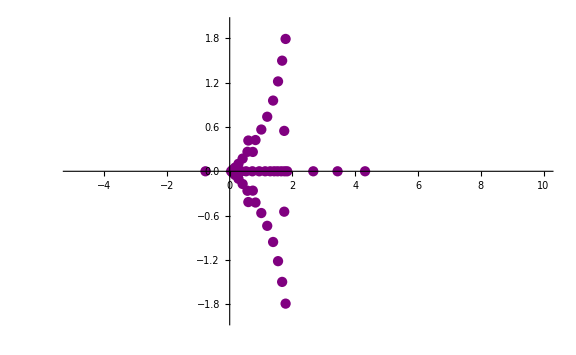

```mathematica
devgRe=Re[devg]
devgIm=Im[devg]
devg2D={devgRe,devgIm}//Transpose;
ListPlot[devg2D,PlotRange->{{-5,10},{-2,2}},PlotStyle->Purple,ImageSize->Large]
```